# SAC fitting

### data loading

```mathematica
p0s={3.85,3.825,3.80};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{ 1, 1, 1,1, 1,60, 80, 200, 500, 800, 1400, 2500, 4200,5000, 6000, 8500, 9500},{ 1, 1, 1,1, 1,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 999999,999999},{ 1, 1, 1,1, 1,40 ,70 ,150 ,250, 600 ,999999, 999999 ,999999, 999999}};
```

```mathematica
tg={0.00007493513959359142,0.0005292353823088456,0.0021126581652639227,0.009308728608198327};
```

```mathematica
SAC=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p","/SACtime_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]
],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
Table[Dimensions[SAC[[1,T]]],{T,Length[temperatures[[1]]]}]
```

{{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{8},{9}}

```mathematica
fitStartPos=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
fitEndPos=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
betaConstraints=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
plateauConstraints=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
tauConstraints=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
fittings=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
initialPlateau=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
initialBeta=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
initialTau=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
betaResults=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
tauAlphaResults=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
plateauResults=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
numExp=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
noiseLevel=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
tauAlpha={{1.1830.014,5.60.6,8.91.1,23.4.,33.4.,52.4.,70.8.,185.19.,470.41.,929.84.,1389.113.,3734.449.,7188.896.,9930.697.,2.040.1810^4,2.90.410^4,4.10.510^4},{0.7900.028,2.290.33,3.00.5,8.20.6,18.61.7,26.72.3,38.92.7,53.81.7,86.8.,117.10.,170.24.,250.27.,478.55.,1166.99.,4460.663.,1.300.2810^4},{0.8120.017,2.760.25,3.930.30,5.50.5,13.31.6,39.4.,62.9.,114.14.,225.35.,550.46.,1423.279.,2572.497.,4591.765.,8.31.210^3}};
```

```mathematica
plateauGold={{0.160.04,0.0920.032,0.0700.012,0.03540.0033,0.02990.0032,0.01840.0009,0.01600.0012,0.00840.0006,0.004900.00034,0.003370.00023,0.00380.0004,0.003320.00032,0.002450.00033,0.002010.00032,0.001970.00033,0.001890.00023,0.00180.0004},{0.210.04,0.170.04,0.150.04,0.1000.008,0.0780.005,0.0700.004,0.0560.007,0.04650.0015,0.03970.0015,0.03100.0013,0.02420.0009,0.02060.0005,0.014040.00031,0.010390.00015,0.006230.00006,0.0038640.000028},{0.2090.026,0.2000.012,0.1830.028,0.1640.012,0.1370.013,0.1020.004,0.08540.0016,0.07120.0010,0.05860.0010,0.04820.0005,0.03510.0007,0.035060.00022,0.026820.00008,0.021890.00006}};
```

## Final results

### fitting results

```mathematica
fittings
```

{{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}},{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}},{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}}

```mathematica
fittings={{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}},{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}},{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}};
```

### fitting parameters

```mathematica
tauAlphaResults=Table[Table[Around[Mean[Table[fittings[[p,T,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[p,T]]]}]],StandardDeviation[Table[fittings[[p,T,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[p,T]]]}]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
plateauResults=Table[Table[Around[Mean[Table[fittings[[p,T,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[p,T]]]}]],StandardDeviation[Table[fittings[[p,T,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[p,T]]]}]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
betaResults=Table[Table[Around[Mean[Table[fittings[[p,T,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[p,T]]]}]],StandardDeviation[Table[fittings[[p,T,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[p,T]]]}]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

{{1.90.4,4.00.4,5.61.0,10.92.2,14.32.2,22.4.,32.9.,82.22.,132.54.,170.177.,291.320.,301.247.,274.76.,350.173.,470.197.,883.870.,1544.325.},{1.570.20,1.980.24,2.310.22,4.50.9,7.41.4,9.51.3,12.42.2,18.4.,27.4.,37.7.,46.13.,77.8.,101.33.,322.160.,850.312.,1.91.110^3},{1.590.09,2.30.4,2.880.29,3.70.7,6.00.9,11.62.0,18.33.0,26.5.,40.10.,100.29.,162.17.,264.54.,535.177.,931.337.}}

{{0.150.05,0.0900.014,0.0680.008,0.0380.008,0.0320.005,0.02110.0023,0.01630.0022,0.00850.0026,0.00590.0012,0.00540.0017,0.00450.0018,0.00380.0015,0.00240.0007,0.00200.0010,0.00180.0004,0.00190.0005,0.00130.0004},{0.1540.013,0.1750.027,0.1570.024,0.1150.026,0.0830.010,0.0680.008,0.0560.005,0.0460.009,0.0360.004,0.03030.0019,0.02480.0025,0.01960.0015,0.01500.0025,0.01060.0027,0.00670.0009,0.00420.0009},{0.1930.013,0.200.04,0.1800.022,0.1640.025,0.1390.018,0.0990.009,0.0850.009,0.0690.005,0.0580.008,0.0480.006,0.03140.0018,0.03000.0034,0.02660.0035,0.02260.0031}}

```mathematica
plateauResults={{0.150.05,0.0900.014,0.0680.008,0.0380.008,0.0320.005,0.02110.0023,0.01630.0022,0.00850.0026,0.00590.0012,0.00540.0017,0.00450.0018,0.00380.0015,0.00240.0007,0.00200.0010,0.00180.0004,0.00190.0005,0.00130.0004},{0.1540.013,0.1750.027,0.1570.024,0.1150.026,0.0830.010,0.0680.008,0.0560.005,0.0460.009,0.0360.004,0.03030.0019,0.02480.0025,0.01960.0015,0.01500.0025,0.01060.0027,0.00670.0009,0.00420.0009},{0.1930.013,0.200.04,0.1800.022,0.1640.025,0.1390.018,0.0990.009,0.0850.009,0.0690.005,0.0580.008,0.0480.006,0.03140.0018,0.03000.0034,0.02660.0035,0.02260.0031}}
```

{{0.150.05,0.0900.014,0.0680.008,0.0380.008,0.0320.005,0.02110.0023,0.01630.0022,0.00850.0026,0.00590.0012,0.00540.0017,0.00450.0018,0.00380.0015,0.00240.0007,0.00200.0010,0.00180.0004,0.00190.0005,0.00130.0004},{0.1540.013,0.1750.027,0.1570.024,0.1150.026,0.0830.010,0.0680.008,0.0560.005,0.0460.009,0.0360.004,0.03030.0019,0.02480.0025,0.01960.0015,0.01500.0025,0.01060.0027,0.00670.0009,0.00420.0009},{0.1930.013,0.200.04,0.1800.022,0.1640.025,0.1390.018,0.0990.009,0.0850.009,0.0690.005,0.0580.008,0.0480.006,0.03140.0018,0.03000.0034,0.02660.0035,0.02260.0031}}

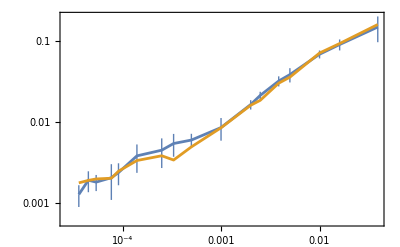
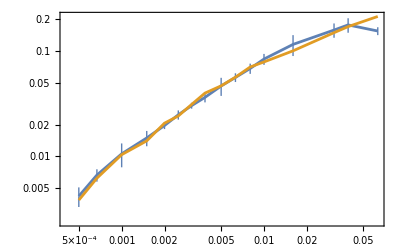
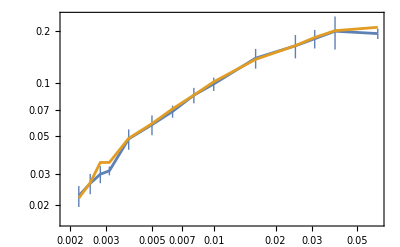

```mathematica
Table[ListLogLogPlot[{Table[{temperatures[[p,T]],plateauResults[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],plateauGold[[p,T,1]]},{T,Length[temperatures[[p]]]}]},Joined->True],{p,Length[p0s]}]
```

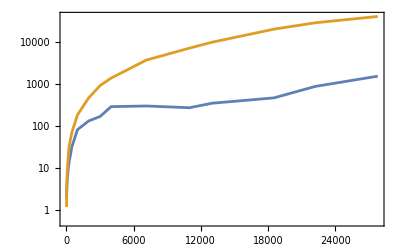
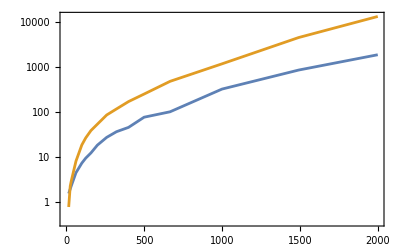
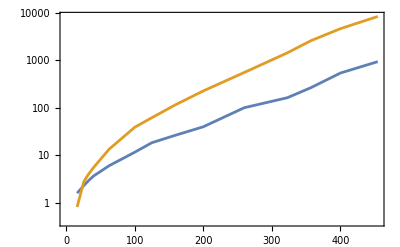

```mathematica
Table[ListLogPlot[{Table[{1/temperatures[[p,T]],tauAlphaResults[[p,T,1]]},{T,Length[temperatures[[p]]]}],Table[{1/temperatures[[p,T]],tauAlpha[[p,T,1]]},{T,Length[temperatures[[p]]]}]},Joined->True],{p,Length[p0s]}]
```

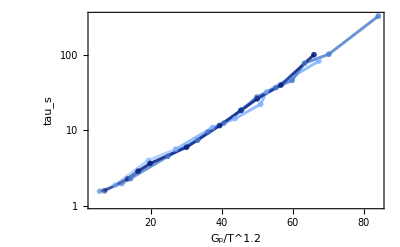

```mathematica
Show[ListLogPlot[Table[Table[{plateauResults[[p,T]][[1]]/temperatures[[p,T]]^1.3,tauAlphaResults[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]}],{p,3}],LabelStyle->Directive[FontSize->20,FontName->"Arial"],PlotMarkers->pm2[4,blueGraient],PlotStyle->blueGraient,FrameLabel->{"\!\(\*SubscriptBox[\(G\), \(p\)]\)/\!\(\*SuperscriptBox[\(T\), \(1.2\)]\) ","tau_s"},ImageSize->400,LabelStyle->Directive[FontSize->14],PlotRange->{All,All},Joined->True],ListLogPlot[Table[Table[{plateauResults[[p,T]][[1]]/temperatures[[p,T]]^1.3,tauAlphaResults[[p,T,1]]},{T,stretchedExpStartEnd[[p,1]],niceStretchedExpStartEnd[[p,2]]}],{p,3}],PlotMarkers->pm1[4,blueGraient],PlotStyle->blueGraient,FrameLabel->{"\!\(\*SubscriptBox[\(G\), \(p\)]\)/\!\(\*SuperscriptBox[\(T\), \(1.3\)]\) ","tau"},ImageSize->600,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs \!\(\*FractionBox[SubscriptBox[\(G\), \(p\)], SuperscriptBox[\(T\), \(1.2\)]]\)",PlotRange->{{2,50},All},Joined->True]]
```

```mathematica
stretchedExpStartEnd={{3,8},{3,14},{3,10}}
```

{{3,8},{3,14},{3,10}}

```mathematica
niceStretchedExpStartEnd={{1,8},{1,14},{1,10}}
```

{{1,8},{1,14},{1,10}}

```mathematica
pm2[8,discreteColScheme]
```

```mathematica
openHexagon=Graphics[{EdgeForm[{Blue,Thickness[0.03]}],FaceForm[None],Polygon[Table[{Cos[θ],Sin[θ]},{θ,0,2 π,π/3}]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,Background->Transparent,ImageSize->20]
```

-Graphics-

```mathematica
greenGraient={RGBColor[0.5,0.8,0.9,0.8],RGBColor[0,0.2,0.5],RGBColor[0.6,0.9,0.6]}
```

{RGBColor[0.5, 0.8, 0.9, 0.8],RGBColor[0, 0.2, 0.5],RGBColor[0.6, 0.9, 0.6]}

```mathematica
blueGraient=Flatten[Table[{RGBColor[0.5,0.7,1,0.6],RGBColor[0.3,0.5,0.8,0.6],RGBColor[0,0.1,0.5,0.6]},{i,4}]]
```

{RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6],RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6],RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6],RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6]}

```mathematica
ColorConvert[blueGraient,"Grayscale"]
```

{GrayLevel[0.6743999999999999, 0.8],GrayLevel[0.4744, 0.8],GrayLevel[0.1744, 0.8],GrayLevel[0.6743999999999999, 0.8],GrayLevel[0.4744, 0.8],GrayLevel[0.1744, 0.8],GrayLevel[0.6743999999999999, 0.8],GrayLevel[0.4744, 0.8],GrayLevel[0.1744, 0.8],GrayLevel[0.6743999999999999, 0.8],GrayLevel[0.4744, 0.8],GrayLevel[0.1744, 0.8]}

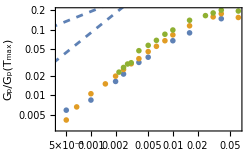

```mathematica
Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],plateauResults[[p,T,1]]},{T,{9,16,14}[[p]]}],{p,3}],PlotMarkers->pm1[6,blueGraient],FrameLabel->{"T ","G_p/G_p(T_max)"},ImageSize->3.5*72,PlotMarkers->Automatic,PlotRange->{All,All},Joined->False],LogLogPlot[90x,{x,0.00001,0.1},PlotStyle->Dashed],LogLogPlot[6x^0.5,{x,0.00001,0.1},PlotStyle->Dashed]]
```

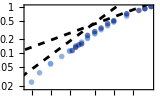

```mathematica
gpInset=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],plateauResults[[p,T,1]]/plateauResults[[p,{1,2,2}[[p]],1]]},{T,2,{8,16,14}[[p]]}],{p,3}],RotateLabel->False,PlotMarkers->pm1[8,blueGraient],Joined->False,PlotStyle->blueGraient,(*FrameLabel->{"T ","G_p/G_p(T=0.039)"}*)LabelStyle->Directive[FontSize->24,FontName->"Arial"],ImageSize->160,PlotMarkers->Automatic,PlotRange->{All,All},Joined->False,FrameTicks->{{{{0.1,0.1,0.05},{0.02,None,0.02},{0.03,None,0.02},{0.04,None,0.02},{0.05,None,0.02},{0.06,None,0.02},{0.07,None,0.02},{0.08,None,0.02},{0.09,None,0.02},{0.2,None,0.02},{0.3,None,0.02},{0.4,None,0.02},{0.5,None,0.02},{0.6,None,0.02},{0.7,None,0.02},{0.8,None,0.02},{0.9,None,0.02},{1,1,0.05}},None},{{{0.001,0.001,0.05},{0.002,None,0.02},{0.003,None,0.02},{0.004,None,0.02},{0.005,None,0.02},{0.006,None,0.02},{0.007,None,0.02},{0.008,None,0.02},{0.009,None,0.02},{0.02,None,0.02},{0.03,None,0.02},{0.04,None,0.02},{0.05,None,0.02},{0.06,None,0.02},{0.07,None,0.02},{0.08,None,0.02},{0.09,None,0.02},{0.01,0.01,0.05}},None}}],LogLogPlot[90x,{x,0.00001,0.1},PlotStyle->{Black,Dashed}],LogLogPlot[6x^0.5,{x,0.00001,0.1},PlotStyle->{Black,Dashed}]]
```

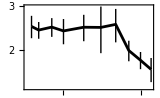
```mathematica
gp3=-Graphics-;
```

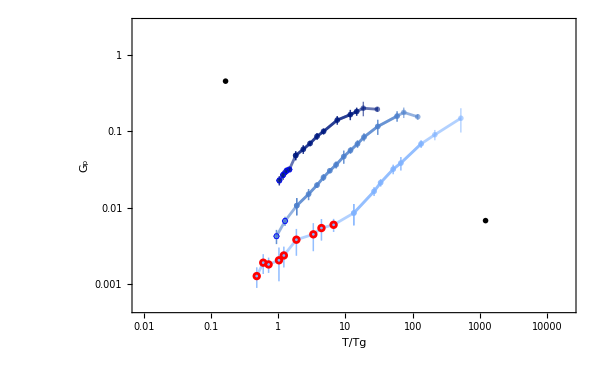

```mathematica
gpPlot=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p]],plateauResults[[p,T]]},{T,niceStretchedExpStartEnd[[p,1]],Length[temperatures[[p]]]}],{p,1,3}],PlotMarkers->pm2[9,blueGraient],Epilog->{{Inset[gpInset,{7.1,-5.},Automatic]},{Inset[gp3,{-1.8,-0.8},Automatic]}},PlotStyle->blueGraient,FrameLabel->{"T/Tg","G_p"},PlotRange->{{0.009,20000},{0.0005,2.5}},LabelStyle->Directive[FontSize->24,FontName->"Arial"],Joined->True,ImageSize->600(*,PlotLabel->"G_p vs T/Tg for different p0", PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,3}]*),FrameTicks->{{{{0.001,0.001,0.025},{0.002,None,0.01},{0.003,None,0.01},{0.004,None,0.01},{0.005,None,0.01},{0.006,None,0.01},{0.007,None,0.01},{0.008,None,0.01},{0.009,None,0.01},{0.01,0.01,0.025},{0.02,None,0.01},{0.03,None,0.01},{0.04,None,0.01},{0.05,None,0.01},{0.06,None,0.01},{0.07,None,0.01},{0.08,None,0.01},{0.09,None,0.01},{0.1,0.1,0.025},{0.2,None,0.01},{0.3,None,0.01},{0.4,None,0.01},{0.5,None,0.01},{0.6,None,0.01},{0.7,None,0.01},{0.8,None,0.01},{0.9,None,0.01},{1,1,0.025},{2,None,0.01},{3,None,0.01},{4,None,0.01},{5,None,0.01},{6,None,0.01},{7,None,0.01},{8,None,0.01},{9,None,0.01}},None},{{{0.01,0.01,0.025},{0.02,None,0.01},{0.03,None,0.01},{0.04,None,0.01},{0.05,None,0.01},{0.06,None,0.01},{0.07,None,0.01},{0.08,None,0.01},{0.09,None,0.01},{0.1,0.1,0.025},{0.2,None,0.01},{0.3,None,0.01},{0.4,None,0.01},{0.5,None,0.01},{0.6,None,0.01},{0.7,None,0.01},{0.8,None,0.01},{0.9,None,0.01},{1,1,0.025},{2,None,0.01},{3,None,0.01},{4,None,0.01},{5,None,0.01},{6,None,0.01},{7,None,0.01},{8,None,0.01},{9,None,0.01},{10,10,0.025},{20,None,0.01},{30,None,0.01},{40,None,0.01},{50,None,0.01},{60,None,0.01},{70,None,0.01},{80,None,0.01},{90,None,0.01},{100,100,0.025},{200,None,0.01},{300,None,0.01},{400,None,0.01},{500,None,0.01},{600,None,0.01},{700,None,0.01},{800,None,0.01},{900,None,0.01},{1000,1000,0.025},{2000,None,0.01},{3000,None,0.01},{4000,None,0.01},{5900,None,0.01},{6000,None,0.01},{7000,None,0.01},{8000,None,0.01},{9000,None,0.01},{10000,10000,0.025}},None}}],ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p]],plateauResults[[p,T]]},{T,stretchedExpStartEnd[[p,1]],stretchedExpStartEnd[[p,2]]}],{p,1,3}],PlotMarkers->pm1[9,blueGraient],PlotStyle->blueGraient,FrameLabel->{"T/Tg","G_p"},PlotRange->{{0.21,600},{0.001,0.3}},Joined->True,ImageSize->600,PlotLabel->"G_p vs T/Tg for different p0", LabelStyle->Directive[FontSize->20,FontName->"Arial"](*,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,3}]*)],ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p]],plateauResults[[p,T]]},{T,niceStretchedExpStartEnd[[p,2]],Length[temperatures[[p]]]}],{p,1,3}],PlotMarkers->pm1[6,blueGraient],PlotStyle->blueGraient,FrameLabel->{"Tg/T","G_p "}],ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p]],plateauResults[[p,T,1]]},{T,Length[temperatures[[p]]]-{8,1,3}[[p]],Length[temperatures[[p]]]}],{p,1,1}],FrameLabel->{"G_p/T ","tau"},LabelStyle->Directive[FontSize->20,FontName->"Arial"],ImageSize->600,PlotMarkers->{Graphics[{Red,Circle[]}],0.05},PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T"(*PlotLegends->{"Noisy data"}*),PlotRange->{{2,14},All},Joined->False],ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p]],plateauResults[[p,T,1]]},{T,Length[temperatures[[p]]]-{8,1,3}[[p]],Length[temperatures[[p]]]}],{p,2,3}],FrameLabel->{"G_p/T ","tau"},LabelStyle->Directive[FontSize->20,FontName->"Arial"],ImageSize->600,PlotMarkers->{openHexagon,0.07},PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T"(*PlotLegends->{"hexatic phase"}*),PlotRange->{{2,14},All},Joined->False](*LogLogPlot[0.0002x,{x,0.1,600},PlotStyle->Dashed],LogLogPlot[0.06x^0.5,{x,0.1,200},PlotStyle->Dashed]*)]
```

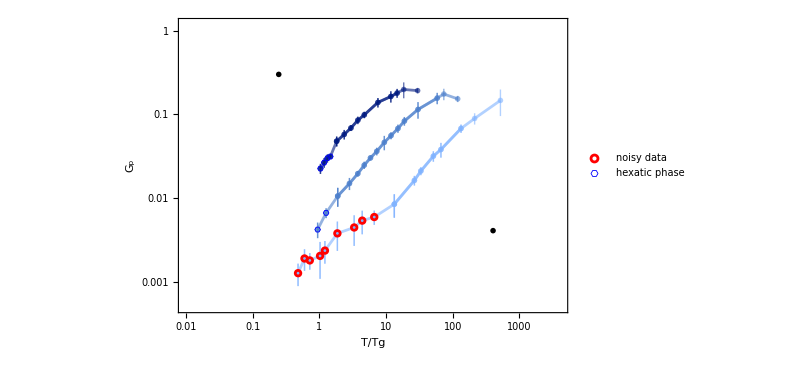

```mathematica
barPLot=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p]],plateauResults[[p,T]]},{T,niceStretchedExpStartEnd[[p,1]],Length[temperatures[[p]]]}],{p,1,3}],PlotMarkers->pm2[9,blueGraient],Epilog->{{Inset[gpInset,{6,-5.5},Automatic]},{Inset[gp3,{-1.4,-1.2},Automatic]}},PlotStyle->blueGraient,FrameLabel->{"T/Tg","G_p"},PlotRange->{{0.01,4100},{0.0005,1.2}},LabelStyle->Directive[FontSize->24,FontName->"Arial"],Joined->True,ImageSize->600(*,PlotLabel->"G_p vs T/Tg for different p0", PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,3}]*)],ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p]],plateauResults[[p,T]]},{T,stretchedExpStartEnd[[p,1]],stretchedExpStartEnd[[p,2]]}],{p,1,3}],PlotMarkers->pm1[9,blueGraient],PlotStyle->blueGraient,FrameLabel->{"T/Tg","G_p"},PlotRange->{{0.21,600},{0.001,0.3}},Joined->True,ImageSize->600,PlotLabel->"G_p vs T/Tg for different p0", LabelStyle->Directive[FontSize->20,FontName->"Arial"],PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,3}]],ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p]],plateauResults[[p,T]]},{T,niceStretchedExpStartEnd[[p,2]],Length[temperatures[[p]]]}],{p,1,3}],PlotMarkers->pm1[6,blueGraient],PlotStyle->blueGraient,FrameLabel->{"Tg/T","G_p "}],ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p]],plateauResults[[p,T,1]]},{T,Length[temperatures[[p]]]-{8,1,3}[[p]],Length[temperatures[[p]]]}],{p,1,1}],FrameLabel->{"G_p/T ","tau"},LabelStyle->Directive[FontSize->20,FontName->"Arial"],ImageSize->600,PlotMarkers->{Graphics[{Red,Circle[]}],0.05},PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T",PlotLegends->{"noisy data"},PlotRange->{{2,14},All},Joined->False],ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p]],plateauResults[[p,T,1]]},{T,Length[temperatures[[p]]]-{8,1,3}[[p]],Length[temperatures[[p]]]}],{p,2,3}],FrameLabel->{"G_p/T ","tau"},LabelStyle->Directive[FontSize->20,FontName->"Arial"],ImageSize->600,PlotMarkers->{openHexagon,0.07},PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T",PlotLegends->{"hexatic phase"},PlotRange->{{2,14},All},Joined->False](*LogLogPlot[0.0002x,{x,0.1,600},PlotStyle->Dashed],LogLogPlot[0.06x^0.5,{x,0.1,200},PlotStyle->Dashed]*)]
```

```mathematica
imageInch=72.;
```

```mathematica
gpfit=FittedModel[…];
```

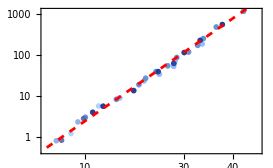

```mathematica
gpT12Plot=Show[ListLogPlot[Table[Table[{plateauResults[[p,T]][[1]]/temperatures[[p,T]]^1.2,tauAlpha[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]}],{p,3}],LabelStyle->Directive[FontSize->24,FontName->"Arial"],PlotMarkers->pm2[9,blueGraient],PlotStyle->blueGraient,ImageSize->3.8imageInch,LabelStyle->Directive[FontSize->14],PlotRange->{{2,45},All},Joined->False,FrameTicks->{{{{0.2,None,0.015},{0.3,None,0.015},{0.4,None,0.015},{0.5,None,0.015},{0.6,None,0.015},{0.7,None,0.015},{0.8,None,0.015},{0.9,None,0.015},{1,1,0.035},{2,None,0.015},{3,None,0.015},{4,None,0.015},{5,None,0.015},{6,None,0.015},{7,None,0.015},{8,None,0.015},{9,None,0.015},{10,10,0.035},{20,None,0.015},{30,None,0.015},{40,None,0.015},{50,None,0.015},{60,None,0.015},{70,None,0.015},{80,None,0.015},{90,None,0.015},{100,"10^2",0.035},{200,None,0.015},{300,None,0.015},{400,None,0.015},{500,None,0.015},{600,None,0.015},{700,None,0.015},{800,None,0.015},{900,None,0.015},{1000,"10^3",0.035},{2000,None,0.015},{3000,None,0.015},{4000,None,0.015},{5000,None,0.015},{6000,None,0.015},{700,None,0.015},{8000,None,0.015},{9000,None,0.015}},None},{{{2,None,0.015},{4,None,0.015},{6,None,0.015},{8,None,0.015},{10,10,0.035},{12,None,0.015},{14,None,0.015},{16,None,0.015},{18,None,0.015},{20,20,0.035},{22,None,0.015},{24,None,0.015},{26,None,0.015},{28,None,0.015},{30,30,0.035},{32,None,0.015},{34,None,0.015},{36,None,0.015},{38,None,0.015},{40,40,0.035},{42,None,0.015},{44,None,0.015},{46,None,0.015},{48,None,0.015},{40,40,0.035}},None}}],ListLogPlot[Table[Table[{plateauResults[[p,T]][[1]]/temperatures[[p,T]]^1.2,tauAlpha[[p,T,1]]},{T,stretchedExpStartEnd[[p,1]],niceStretchedExpStartEnd[[p,2]]}],{p,3}],PlotMarkers->pm1[9,blueGraient],PlotStyle->blueGraient,FrameLabel->{"G_p/T^1.2 ","tau"},ImageSize->600,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T^1.2",PlotRange->{{2,50},All},Joined->False],LogPlot[gpfit[x],{x,0,50},PlotStyle->{Dashed,Red},FrameLabel->{"G_p/T^1.2 ","tau"}]]
```

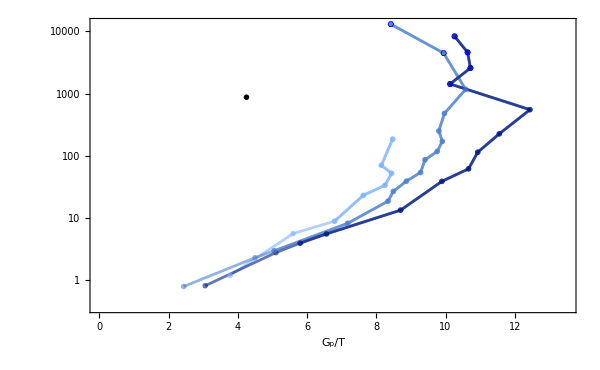

```mathematica
gpTPlot=Show[ListLogPlot[Table[Table[{plateauResults[[p,T]][[1]]/temperatures[[p,T]]^1,tauAlpha[[p,T,1]]},{T,Length[temperatures[[p]]]-{9,0,0}[[p]]}],{p,3}],PlotMarkers->pm2[9,blueGraient],FrameLabel->{"G_p/T "},ImageSize->600,PlotRange->{{0,13.5},All},LabelStyle->Directive[FontSize->24,FontName->"Arial"],PlotStyle->blueGraient,Joined->True,Epilog->{Inset[gpT12Plot,{4.25,6.77},Automatic]},FrameTicks->{{{{0.2,None,0.01},{0.3,None,0.01},{0.4,None,0.01},{0.5,None,0.01},{0.6,None,0.01},{0.7,None,0.01},{0.8,None,0.01},{0.9,None,0.01},{1,1,0.02},{2,None,0.01},{3,None,0.01},{4,None,0.01},{5,None,0.01},{6,None,0.01},{7,None,0.01},{8,None,0.01},{9,None,0.01},{10,10,0.02},{20,None,0.01},{30,None,0.01},{40,None,0.01},{50,None,0.01},{60,None,0.01},{70,None,0.01},{80,None,0.01},{90,None,0.01},{100,"10^2",0.02},{200,None,0.01},{300,None,0.01},{400,None,0.01},{500,None,0.01},{600,None,0.01},{700,None,0.01},{800,None,0.01},{900,None,0.01},{1000,"10^3",0.02},{2000,None,0.01},{3000,None,0.01},{4000,None,0.01},{5000,None,0.01},{6000,None,0.01},{7000,None,0.01},{8000,None,0.01},{9000,None,0.01},{10000,"10^4",0.02},{20000,None,0.01},{30000,None,0.01}},None},{{{0,0,0.02},{1,None,0.01},{2,2,0.02},{3,None,0.01},{4,4,0.02},{5,None,0.01},{6,6,0.02},{7,None,0.01},{8,8,0.02},{9,None,0.01},{10,10,0.02},{11,None,0.01},{12,12,0.02},{13,None,0.01},{14,14,0.02}},None}}],ListLogPlot[Table[Table[{plateauResults[[p,T]][[1]]/temperatures[[p,T]]^1,tauAlpha[[p,T,1]]},{T,stretchedExpStartEnd[[p,1]],Length[temperatures[[p]]]-{9,0,0}[[p]]}],{p,3}],PlotMarkers->pm1[9,blueGraient],PlotStyle->blueGraient,LabelStyle->Directive[FontSize->24,FontName->"Arial"],FrameLabel->{"G_p/T^1.2 ","tau"},ImageSize->600,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T^1.2",(*PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],*)PlotRange->{{2,50},All},Joined->True],ListLogPlot[Table[Table[{plateauResults[[p,T]][[1]]/temperatures[[p,T]]^1,tauAlpha[[p,T,1]]},{T,Length[temperatures[[p]]]-{7,1,3}[[p]],Length[temperatures[[p]]]}],{p,2,3}],LabelStyle->Directive[FontSize->20,FontName->"Arial"],FrameLabel->{"G_p/T ","tau"},ImageSize->600,PlotMarkers->{openHexagon,0.07},PlotLabel->"tau vs G_p/T"(*,PlotLegends->{"hexatic phase"}*),PlotRange->{{2,14},All},Joined->False]]
```

```mathematica
Export["/home/chengling/Research/updates/07282024/gpTPLot.jpeg",Grid[Partition[{gpTPlot,gpT12Plot},2]],ImageResolution->300]
```

/home/chengling/Research/updates/07282024/gpTPLot.jpeg

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/tauGpTPLot.jpeg",gpTPlot,ImageResolution->400]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/tauGpTPLot.jpeg

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/tauGpTInset.png",gpT12Plot,ImageResolution->400]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/tauGpTInset.png

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/gpTPLotwithP3.jpeg",gpPlot,ImageResolution->400]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/gpTPLotwithP3.jpeg

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/gpTPLotBar.jpeg",barPLot,ImageResolution->400]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/gpTPLotBar.jpeg

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/gpTInset.png",gpInset,ImageResolution->400]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/gpTInset.png

## p_0=3.85

### T=0.000036

```mathematica
temperatures[[1,17]]
```

0.000036

```mathematica
curP=1;curT=17;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,162,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitOffset={161,161,161,161,161,161,161,161,161}+1;
```

```mathematica
fitStartNum={30,20,40,55,40,40,40,35,40}
```

{30,20,40,55,40,40,40,35,40}

```mathematica
fitEndNum={2900,2900,30000,9200,9200,30000,12000,31000,30000}
```

{2900,2900,30000,9200,9200,30000,12000,31000,30000}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2,fitOffset[[i]];;]]],_?(#>fitStartNum[[i]]&)][[1,1]]+fitOffset[[i]],{i,Length[SAC[[curP,curT]]]}]
```

{239,235,243,246,243,243,243,241,243}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2,fitOffset[[i]];;]]],_?(#>fitEndNum[[i]]&)][[1,1]]+fitOffset[[i]],{i,Length[SAC[[curP,curT]]]}]
```

{292,292,319,306,306,319,309,319,319}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.1,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.01>G>0.000001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],4000>τ>1000}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.00161847,0.000989231,0.00132779,0.00147567,0.000724251,0.00071811,0.00155132,0.00126422,0.00174467}

0.00130.0004

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{1526.89,1185.17,1443.14,1821.59,1274.11,1137.01,1736.87,1641.19,2132.13}

1544.325.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.392409,0.571661,0.390884,0.381523,0.560166,0.686861,0.428042,0.37196,0.281805}

0.450.13

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

33.28

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitOffset[[i]],Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.000045

```mathematica
curP=1;curT=16;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,162,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitOffset={161,161,161,161,161,161,161,161,161}+1;
```

```mathematica
fitStartNum={35,35,35,35,35,35,35,35,35,35}
```

{35,35,35,35,35,35,35,35,35,35}

```mathematica
fitEndNum={26000,7200,60000,3000,21000,12000,1600,31000,5200}
```

{26000,7200,60000,3000,21000,12000,1600,31000,5200}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2,fitOffset[[i]];;]]],_?(#>fitStartNum[[i]]&)][[1,1]]+fitOffset[[i]],{i,Length[SAC[[curP,curT]]]}]
```

{241,241,241,241,241,241,241,241}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2,fitOffset[[i]];;]]],_?(#>fitEndNum[[i]]&)][[1,1]]+fitOffset[[i]],{i,Length[SAC[[curP,curT]]]}]
```

{317,302,327,293,316,309,285,319}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.1,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.01>G>0.000001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],4000>τ>100}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.00179829,0.00233329,0.00289003,0.00197236,0.00135173,0.00209389,0.00124103,0.00151552}

0.00190.0005

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{351.511,314.257,1566.81,507.231,632.356,2786.05,340.976,566.264}

883.870.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.306057,0.309782,0.155708,0.385455,0.343991,0.403156,0.594446,0.377567}

0.360.12

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitOffset[[i]],Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.000054

```mathematica
curP=1;curT=15;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,162,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitOffset={161,161,161,161,161,161,161,161,161,161}+1;
```

```mathematica
fitStartNum={35,35,35,35,35,35,35,35,35,35,35}
```

{35,35,35,35,35,35,35,35,35,35,35}

```mathematica
fitEndNum={5000,17000,6000,5000,4000,2000,4000,10000,5900,12000}
```

{5000,17000,6000,5000,4000,2000,4000,10000,5900,12000}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2,fitOffset[[i]];;]]],_?(#>fitStartNum[[i]]&)][[1,1]]+fitOffset[[i]],{i,Length[SAC[[curP,curT]]]}]
```

{241,241,241,241,241,241,241,241,241,241}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2,fitOffset[[i]];;]]],_?(#>fitEndNum[[i]]&)][[1,1]]+fitOffset[[i]],{i,Length[SAC[[curP,curT]]]}]
```

{299,312,301,299,296,288,296,307,301,309}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.1,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.01>G>0.000001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],4000>τ>100}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.00199334,0.00156472,0.00218563,0.00152518,0.00131014,0.00179107,0.00267744,0.00141328,0.00177562,0.00177531}

0.00180.0004

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{397.47,439.39,235.686,477.374,683.478,215.245,273.275,575.815,598.15,803.662}

470.197.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.355397,0.332246,0.380422,0.431792,0.47734,0.629126,0.37822,0.402729,0.491058,0.341336}

0.420.09

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitOffset[[i]],Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.000077

```mathematica
curP=1;curT=14;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,162,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitOffset={161,161,161,161,161,161,161,161,161,161}+1;
```

```mathematica
fitStartNum={35,35,35,35,35,35,35,35,35,35,35}
```

{35,35,35,35,35,35,35,35,35,35,35}

```mathematica
fitEndNum={4600,1800,2500,240,20000,8500,3600,2300,37000,1100}
```

{4600,1800,2500,240,20000,8500,3600,2300,37000,1100}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2,fitOffset[[i]];;]]],_?(#>fitStartNum[[i]]&)][[1,1]]+fitOffset[[i]],{i,Length[SAC[[curP,curT]]]}]
```

{241,241,241,241,241,241,241,241,241,241}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2,fitOffset[[i]];;]]],_?(#>fitEndNum[[i]]&)][[1,1]]+fitOffset[[i]],{i,Length[SAC[[curP,curT]]]}]
```

{298,286,291,263,315,304,294,290,322,281}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.1,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.01>G>0.000001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>100}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.00253654,0.00146554,0.00153338,0.00131427,0.00457343,0.00194444,0.00150108,0.0018518,0.00181407,0.00186423}

0.00200.0010

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{201.843,345.192,337.628,143.35,677.573,403.744,576.246,362.907,151.508,299.912}

350.173.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.345375,0.436538,0.441056,0.810581,0.17904,0.377107,0.38668,0.443893,0.531944,0.71649}

0.470.18

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

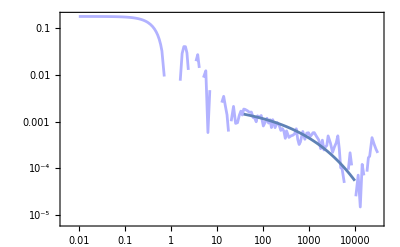
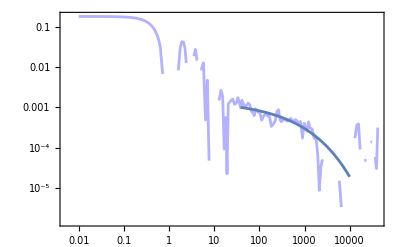
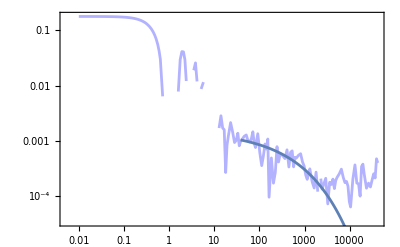
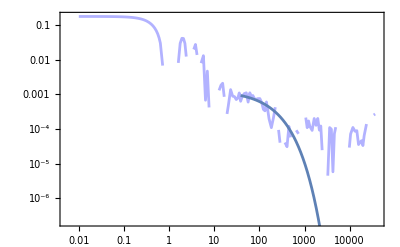
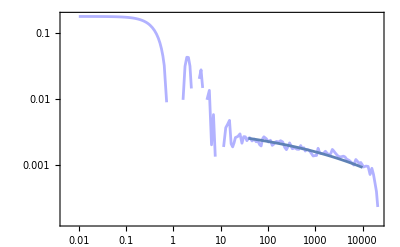
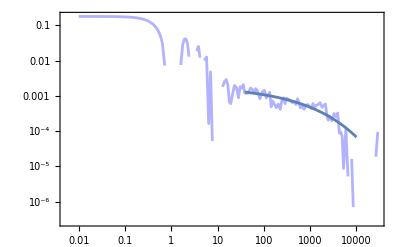
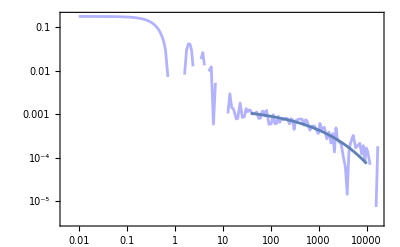
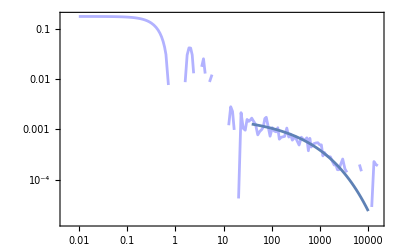

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitOffset[[i]],Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.000091

```mathematica
curP=1;curT=13;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitStartNum={35,35,35,35,35,35,35,35,35,35,35}
```

{35,35,35,35,35,35,35,35,35,35,35}

```mathematica
fitEndNum={2900,4300,9200,3300,3000,4600,490,6600,900,660}
```

{2900,4300,9200,3300,3000,4600,490,6600,900,660}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitStartNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{79,79,79,79,79,79,79,79,79,79}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitEndNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{130,135,144,132,131,136,109,140,116,114}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.1,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.01>G>0.000001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>10}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.00205829,0.0037756,0.00292403,0.00311897,0.0025805,0.00156743,0.00200679,0.00194327,0.00174175,0.00188376}

0.00240.0007

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{273.375,192.501,336.822,176.934,227.11,281.977,212.397,345.185,417.024,273.145}

274.76.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.368016,0.285593,0.314132,0.401269,0.428222,0.393042,0.505608,0.36936,0.532223,0.581874}

0.420.10

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.00014

```mathematica
curP=1;curT=12;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitStartNum={20,20,20,20,20,20,20,20,20,20}
```

{20,20,20,20,20,20,20,20,20,20}

```mathematica
fitEndNum={2500,1300,2500,3300,2900,1800,4900,2100,900,2900}
```

{2500,1300,2500,3300,2900,1800,4900,2100,900,2900}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitStartNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{73,73,73,73,73,73,73,73,73,73}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitEndNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{129,121,129,132,130,124,136,126,116,130}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.1,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.01>G>0.000001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>10}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.00386968,0.00262438,0.0032034,0.00393284,0.00209964,0.00555492,0.00371226,0.00690424,0.00261423,0.0034183}

0.00380.0015

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{217.413,164.816,891.65,119.855,214.281,59.5482,221.399,558.816,316.404,246.001}

301.247.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.275594,0.464958,0.611283,0.323652,0.440638,0.286608,0.340086,0.268851,0.569125,0.377286}

0.400.12

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

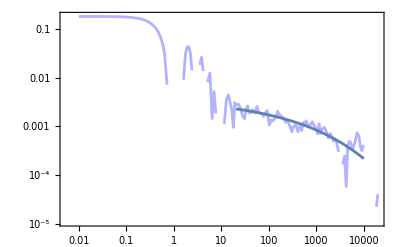
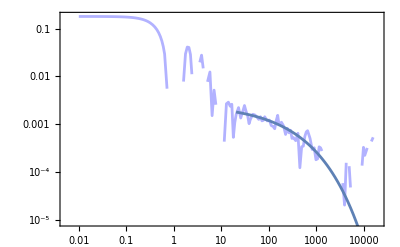
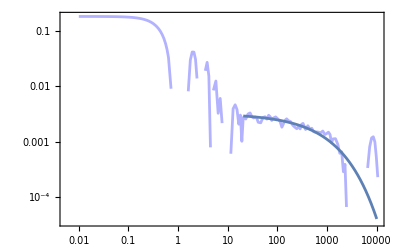
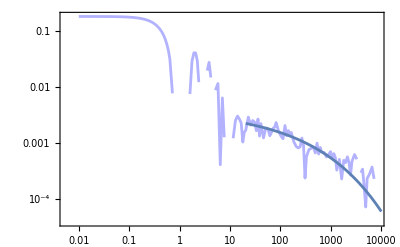
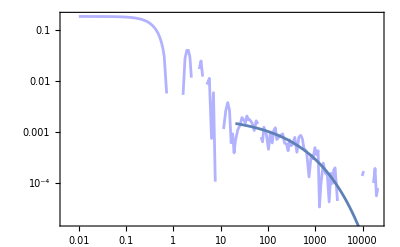
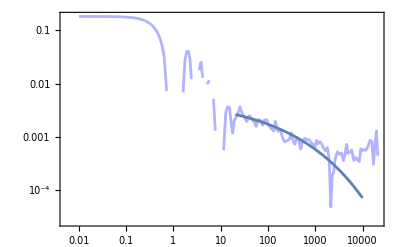
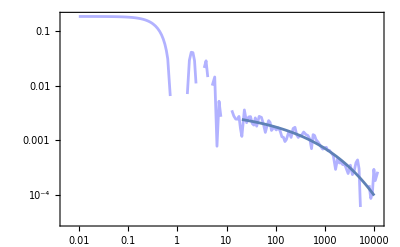
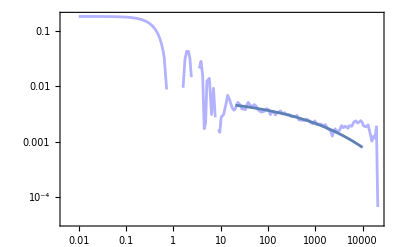

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.00025

```mathematica
curP=1;curT=11;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitStartNum={15,15,15,15,15,15,15,15,15,15}
```

{15,15,15,15,15,15,15,15,15,15}

```mathematica
fitEndNum={160,1100,230,820,1800,610,2900,450,5000,290}
```

{160,1100,230,820,1800,610,2900,450,5000,290}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitStartNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{69,69,69,69,69,69,69,69,69,69}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitEndNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{97,119,101,116,124,112,130,108,137,104}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.1,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.01>G>0.000001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>10}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.00367962,0.00516071,0.00339995,0.00784558,0.00204849,0.00370931,0.00692294,0.0037694,0.00483567,0.00321808}

0.00450.0018

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{64.2609,62.3034,96.6927,372.377,790.165,86.0311,931.025,111.792,300.865,90.0178}

291.320.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.485505,0.371433,0.847794,0.310013,0.94256,0.538598,0.564503,0.595858,0.224516,0.833513}

0.570.24

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.00033

```mathematica
curP=1;curT=10;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitStartNum={15,15,15,15,15,15,15,15,15,15}
```

{15,15,15,15,15,15,15,15,15,15}

```mathematica
fitEndNum={530,270,1100,570,2100,150,410,660,200,410}
```

{530,270,1100,570,2100,150,410,660,200,410}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitStartNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{69,69,69,69,69,69,69,69,69,69}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitEndNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{110,103,119,111,126,96,108,114,99,108}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.1,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.01>G>0.000001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>10}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.00627993,0.0041305,0.00423304,0.00655636,0.00798308,0.00681347,0.00411112,0.00439617,0.0026535,0.0067039}

0.00540.0017

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{59.3105,153.338,600.293,45.9108,60.5547,80.5986,112.228,330.281,217.428,38.3747}

170.177.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.483639,0.93131,0.942498,0.294171,0.242114,0.92267,0.536838,0.862512,0.79019,0.403562}

0.640.28

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

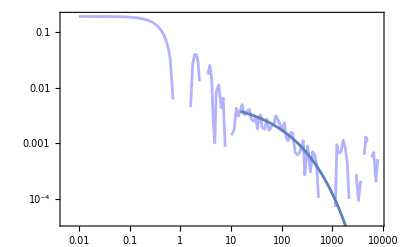
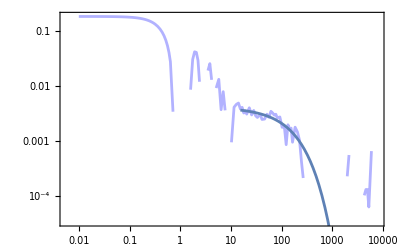
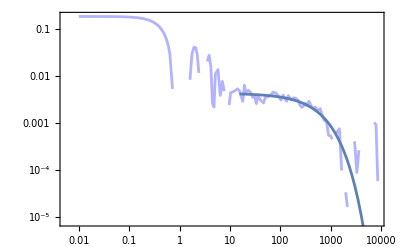
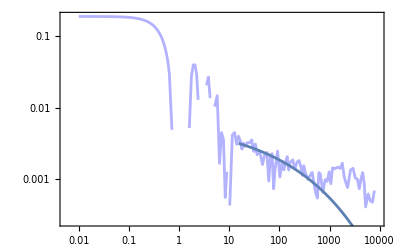
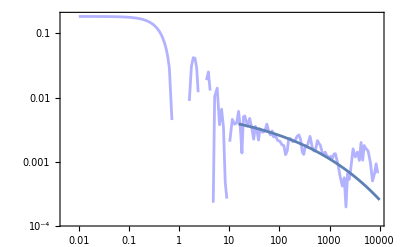
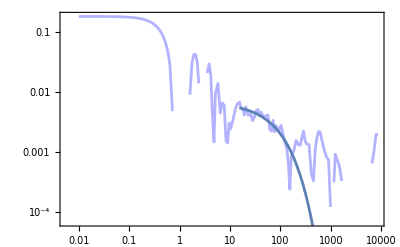
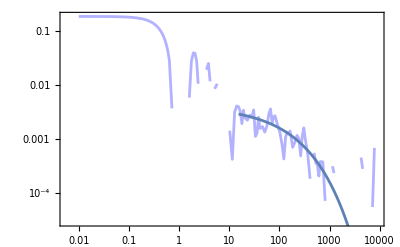
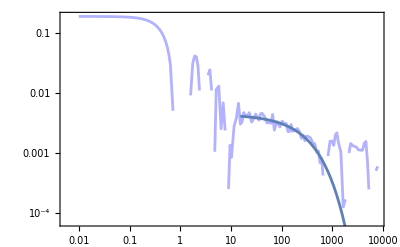

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.0005

```mathematica
curP=1;curT=9;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitStartNum={10,10,10,10,10,10,10,10,10,10}
```

{10,10,10,10,10,10,10,10,10,10}

```mathematica
fitEndNum={660,180,330,410,570,250,450,450,490,820}
```

{660,180,330,410,570,250,450,450,490,820}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitStartNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{65,65,65,65,65,65,65,65,65,65}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitEndNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{114,98,106,108,111,102,108,108,109,116}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.8,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.01>G>0.000001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],200>τ>10}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.00644322,0.00559115,0.00509594,0.00563618,0.00503925,0.00738296,0.00684811,0.00363894,0.00682116,0.00694397}

0.00590.0012

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{166.444,44.5492,130.962,124.735,96.4287,77.8111,198.074,189.026,96.7163,199.455}

132.54.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.857989,0.817508,0.84194,0.724354,0.727802,0.750186,0.930161,0.724991,0.784878,0.719135}

0.790.07

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

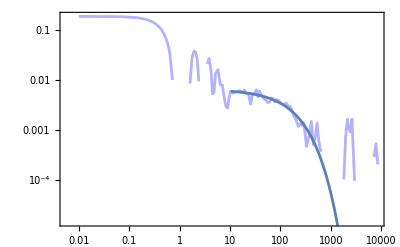
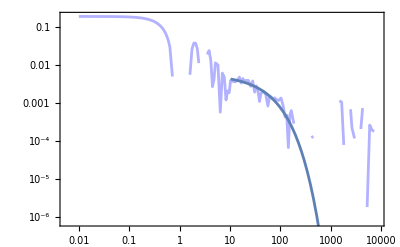
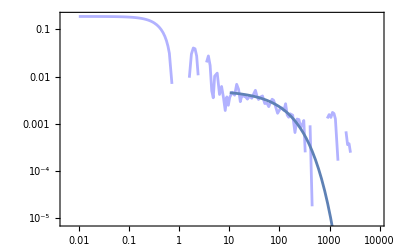
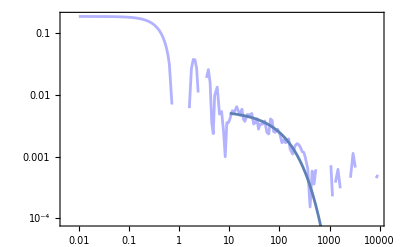
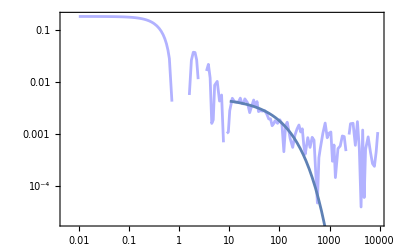
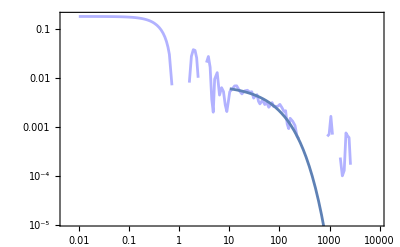
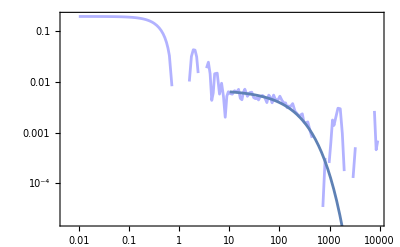
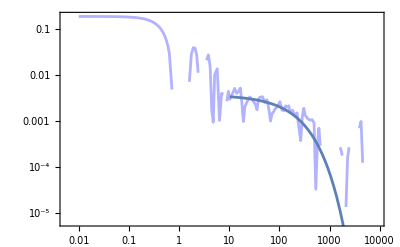

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.001

```mathematica
curP=1;curT=8;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitStartNum={8,8,8,8,8,8,8,8,8,8}
```

{8,8,8,8,8,8,8,8,8,8}

```mathematica
fitEndNum={250,230,200,370,130,150,180,150,130,140}
```

{250,230,200,370,130,150,180,150,130,140}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitStartNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{62,62,62,62,62,62,62,62,62,62}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitEndNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{102,101,99,107,94,96,98,96,94,95}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.8,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.2>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>10}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.00527981,0.0103505,0.0142896,0.00878961,0.00965392,0.00662622,0.00748254,0.0093957,0.00647892,0.0064072}

0.00850.0026

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{79.1162,122.699,92.8807,97.8702,70.8945,103.494,75.6648,56.3778,54.2872,67.7397}

82.22.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.843686,0.990802,0.933495,0.878855,0.970924,0.914169,0.969922,0.947957,0.92049,0.948717}

0.930.04

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

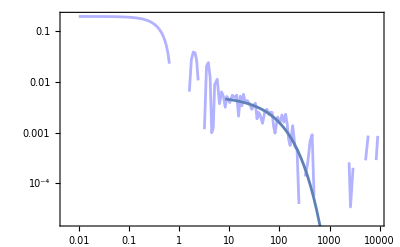
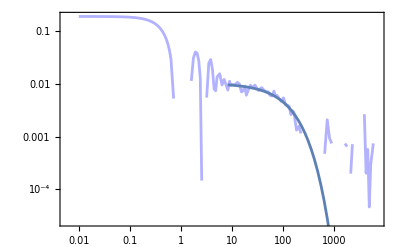
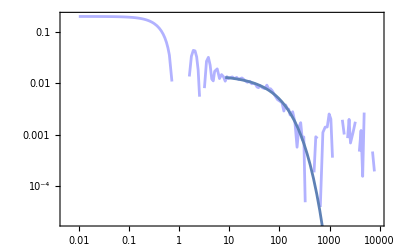
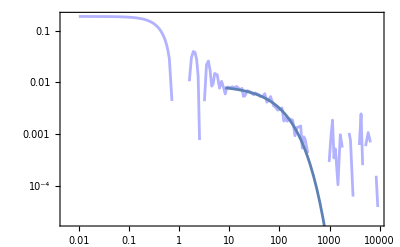
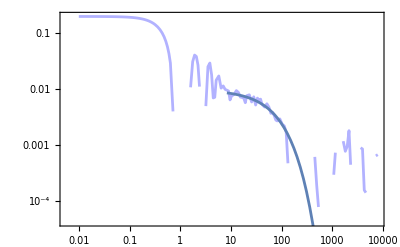
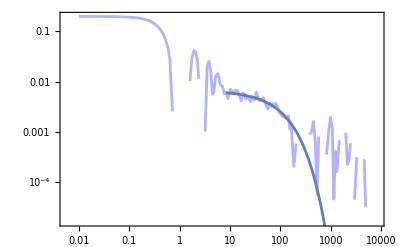
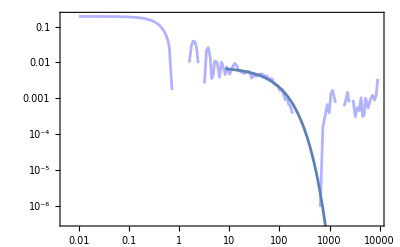
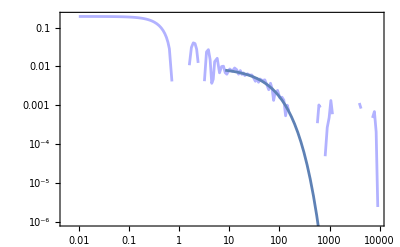

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.002

```mathematica
curP=1;curT=7;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitStartNum={5,5,5,5,5,5,5,5,5,5}
```

{5,5,5,5,5,5,5,5,5,5}

```mathematica
fitEndNum={92,92,120,130,140,120,77,67,130,100}
```

{92,92,120,130,140,120,77,67,130,100}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>6&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{59,59,59,59,59,59,59,59,59,59}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitEndNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{90,90,93,94,95,93,89,87,94,91}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.8,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.1>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>10}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0177281,0.0181891,0.0136622,0.0133225,0.0184917,0.0197008,0.0159774,0.0159205,0.0150661,0.0148604}

0.01630.0022

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{33.6922,14.5029,28.6226,32.6921,27.3358,29.9413,26.8819,25.9374,37.4223,15.7585}

27.7.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.985753,0.808993,0.817336,0.807894,0.805625,0.808471,0.92065,0.921588,0.81935,0.809564}

0.850.07

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.0025

```mathematica
curP=1;curT=6;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitStartNum={5,5,5,5,5,5,5,5,5,5}
```

{5,5,5,5,5,5,5,5,5,5}

```mathematica
fitEndNum={77,46,72,51,67,67,51,67,100,67}
```

{77,46,72,51,67,67,51,67,100,67}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitStartNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{57,57,57,57,57,57,57,57,57,57}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitEndNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{89,82,88,83,87,87,83,87,91,87}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.8,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.5>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],100>τ>10}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0193021,0.0240986,0.0242054,0.0224566,0.0227893,0.0207938,0.0193872,0.0188064,0.0175634,0.0216524}

0.02110.0023

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{17.5636,18.1685,15.1927,23.9867,23.0143,28.8796,19.0544,24.2979,24.6453,26.2951}

22.4.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.81262,0.817528,0.812512,0.805086,0.807536,0.809131,0.950639,0.83886,0.804435,0.80582}

0.830.04

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.00385

```mathematica
curP=1;curT=5;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitStartNum={5,5,5,5,5,5,5,5,5,5}
```

{5,5,5,5,5,5,5,5,5,5}

```mathematica
fitEndNum={67,56,41,38,51,61,41,51,36,31}
```

{67,56,41,38,51,61,41,51,36,31}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitStartNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{57,57,57,57,57,57,57,57,57,57}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitEndNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{87,84,82,80,83,85,82,83,80,78}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.8,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.5>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],100>τ>1}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0231198,0.0365368,0.0286685,0.0338832,0.033574,0.0308429,0.0272331,0.0315045,0.0341645,0.0381669}

0.0320.005

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{14.3824,12.9813,10.1673,12.4566,14.3868,12.4107,13.3568,16.0949,11.9906,8.19921}

12.62.2

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.807199,0.882498,0.804283,0.810299,0.993147,0.804196,0.803177,0.85861,0.813425,0.819292}

0.840.06

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

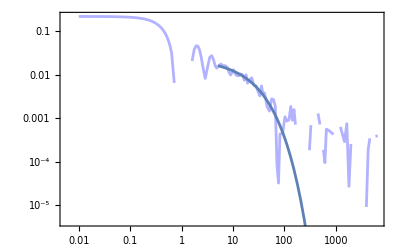
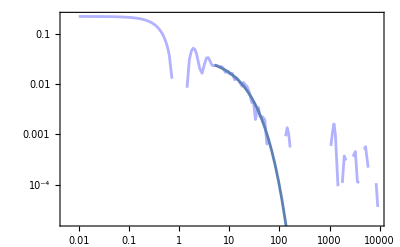
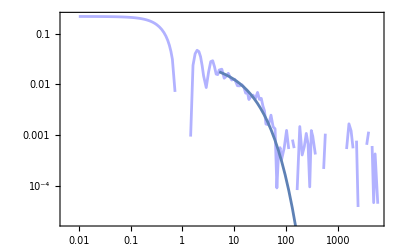
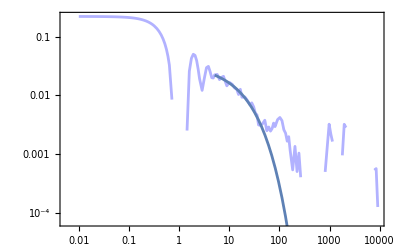
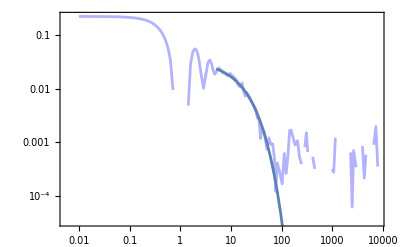
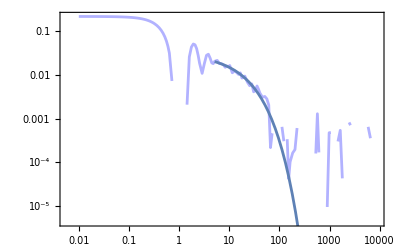
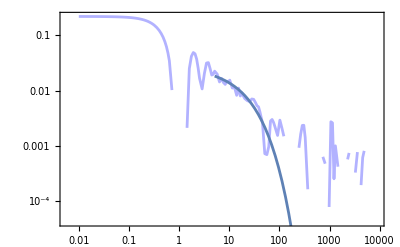
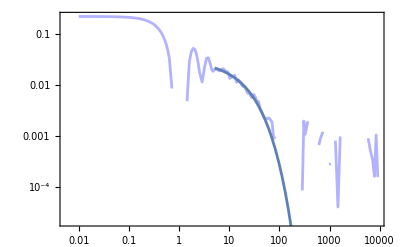

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.005

```mathematica
curP=1;curT=4;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitStartNum={5,5,5,5,5,5,5,5,5,5}
```

{5,5,5,5,5,5,5,5,5,5}

```mathematica
fitEndNum={28,28,31,33,28,36,38,31,36,41}
```

{28,28,31,33,28,36,38,31,36,41}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>6&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{59,59,59,59,59,59,59,59,59,59}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitEndNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{110,103,119,111,126,96,108,114,99,108}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.7,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.5>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],100>τ>1}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0308713,0.0456941,0.0341624,0.0480619,0.0323637,0.032694,0.0322198,0.0313894,0.0461095,0.0476693}

0.0380.008

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{12.8691,13.4847,8.7121,10.1192,12.0843,13.2059,11.3579,13.6472,11.9505,12.1678}

12.01.6

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.991202,0.979235,0.778691,0.878451,0.972819,0.968458,0.916069,0.96182,0.953535,0.973885}

0.940.07

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

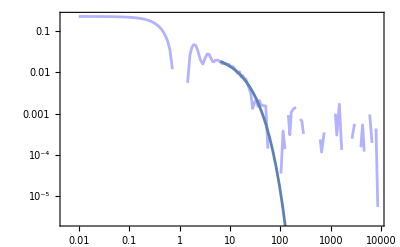
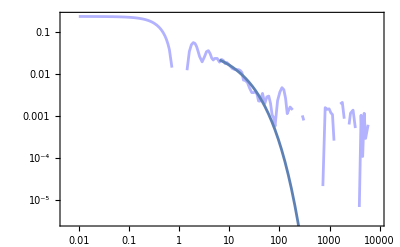
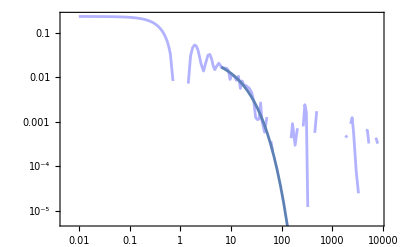
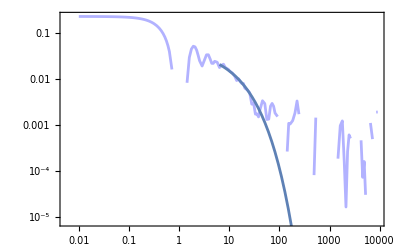
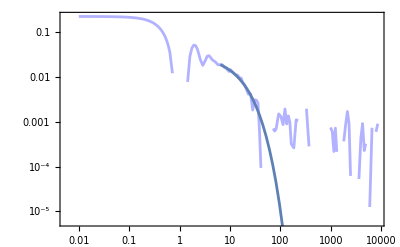
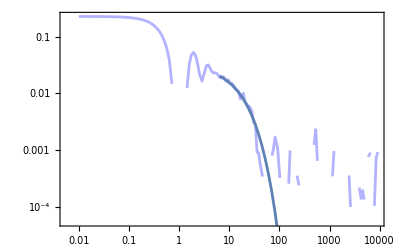
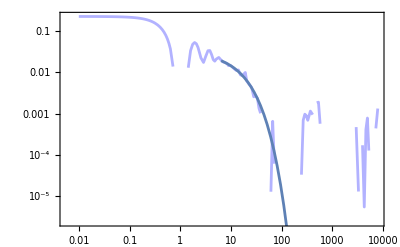
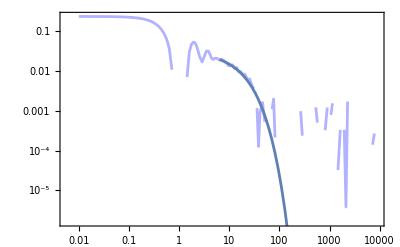

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.01

```mathematica
curP=1;curT=3;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitStartNum={4,4,5,4,5,4,5,5,5,4}
```

{4,4,5,4,5,4,5,5,5,4}

```mathematica
fitEndNum={14,20,26,26,18,28,31,26,20,15}
```

{14,20,26,26,18,28,31,26,20,15}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitStartNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{54,54,57,54,57,54,57,57,57,54}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitEndNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{68,73,76,76,72,76,78,76,73,69}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.8,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.5>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],100>τ>1}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0692834,0.0700321,0.0709384,0.0562414,0.067645,0.0584496,0.0825858,0.0630549,0.074517,0.0668619}

0.0680.008

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{5.46885,5.74891,4.59331,6.52529,4.71432,7.2226,4.61708,6.06404,4.71272,6.64743}

5.61.0

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.922153,0.994359,0.710292,0.977462,0.77839,0.936641,0.799659,0.705394,0.735646,0.992204}

0.860.12

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.016

```mathematica
curP=1;curT=2;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitStartNum={8,4,4,4,4,8,4,4,4,4}
```

{8,4,4,4,4,8,4,4,4,4}

```mathematica
fitEndNum={8,13,12,14,14,8,15,15,28,14}
```

{8,13,12,14,14,8,15,15,28,14}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>4.2&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{55,55,55,55,55,55,55,55,55,55}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitEndNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{62,68,67,68,68,62,69,69,76,68}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.99999,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.5>G>0.07,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],100>τ>1}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0980683,0.0904014,0.105968,0.106117,0.10022,0.0925917,0.0702126,0.0745974,0.0700859,0.0873056}

0.0900.014

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{4.73283,4.60213,3.74522,3.61608,3.58677,4.41353,4.43921,4.38166,4.65809,4.02524}

4.20.4

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995}

0.999994999034

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.039

```mathematica
curP=1;curT=1;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
fitStartNum={3,3,3,3,3,3,3,3,3,3,3}
```

{3,3,3,3,3,3,3,3,3,3,3}

```mathematica
fitEndNum={7,6,8,6,9,8,8,8,8,6}
```

{7,6,8,6,9,8,8,8,8,6}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitStartNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{51,51,51,51,51,51,51,51,51,51}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>fitEndNum[[i]]&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{60,59,62,59,64,62,62,62,62,59}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.99999,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.5>G>0.05,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],100>τ>0.1}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.123442,0.19089,0.0906425,0.194241,0.247132,0.118473,0.160459,0.139063,0.0795945,0.12769}

0.150.05

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{2.23286,1.60835,2.2859,1.54462,1.38559,2.05321,1.68567,1.7757,2.532,1.89109}

1.90.4

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995}

0.999995000110

```mathematica
SAC[[curP,curT,1,2,fitStartPos[[curP,curT,1]]]]
```

38.4

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### loose constrains

#### fitting results

```mathematica
Table[Dimensions[fittings[[1,T]]],{T,Length[temperatures[[2]]]}]
```

{{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{8}}

```mathematica
fittings[[1]]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
fittings[[1]]={{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}};
```

#### fitting parameters

```mathematica
curP=1;
```

```mathematica
tauAlphaResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}];
plateauResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}];
betaResults[[curP]]=Join[Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}]];
```

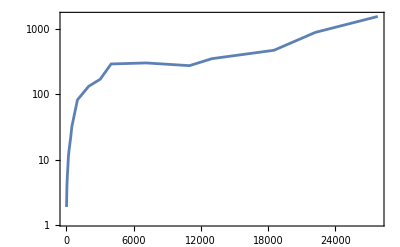

```mathematica
ListLogPlot[Table[{1/temperatures[[curP,T]],tauAlphaResults[[curP,T,1]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

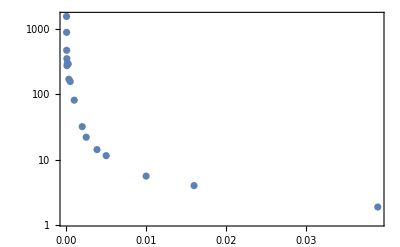

```mathematica
ListLogPlot[Table[{temperatures[[curP,T]],tauAlphaResults[[curP,T,1]]},{T,Length[temperatures[[curP]]]}],Joined->False,PlotRange->All]
```

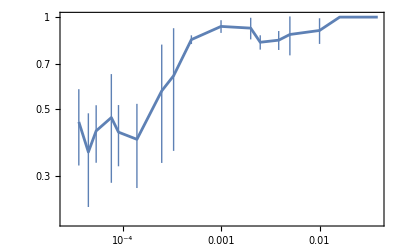

```mathematica
ListLogLogPlot[Table[{temperatures[[curP,T]],betaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

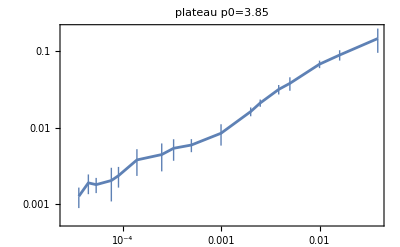

```mathematica
ListLogLogPlot[{Table[{temperatures[[curP,T]],plateauResults[[curP,T]]},{T,Length[temperatures[[curP]]]}]},PlotRange->All,Joined->True,PlotLabel->"plateau p0="<>ToString[p0s[[curP]]]]
```

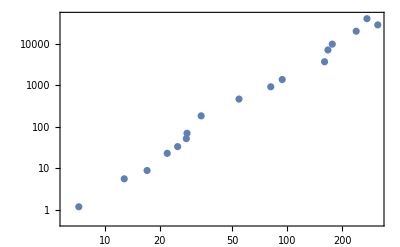

```mathematica
ListLogLogPlot[{Table[{plateauResults[[curP,T,1]]/temperatures[[curP,T]]^1.2,tauAlpha[[curP,T]]},{T,Length[temperatures[[curP]]]}]},PlotRange->All,Joined->False]
```

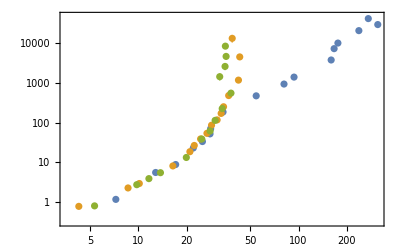

```mathematica
ListLogLogPlot[{Table[{plateauResults[[curP,T,1]]/temperatures[[curP,T]]^1.2,tauAlpha[[curP,T]]},{T,Length[temperatures[[curP]]]}],Table[{plateauResults[[2,T,1]]/temperatures[[2,T]]^1.2,tauAlpha[[2,T]]},{T,Length[temperatures[[2]]]}],Table[{plateauResults[[3,T,1]]/temperatures[[3,T]]^1.2,tauAlpha[[3,T]]},{T,Length[temperatures[[3]]]}]},PlotRange->All,Joined->False]
```

## p_0=3.825

### T=0.0005

```mathematica
curP=2;curT=16;
```

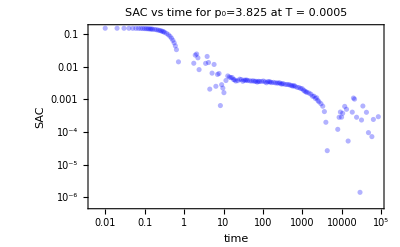
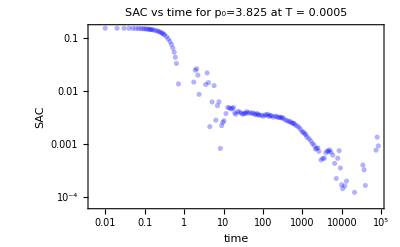
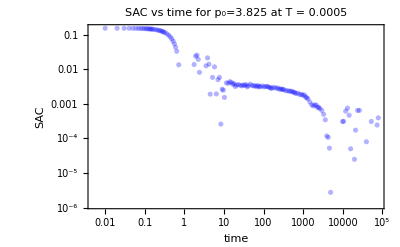
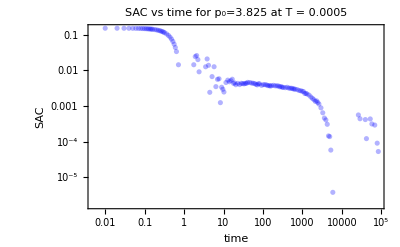
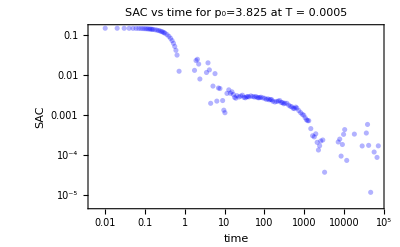
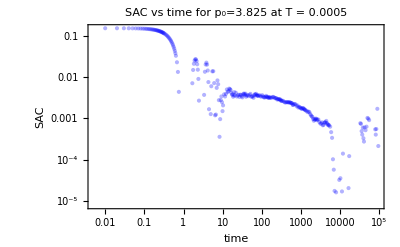
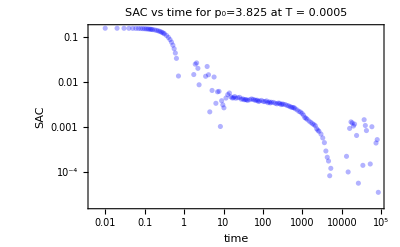
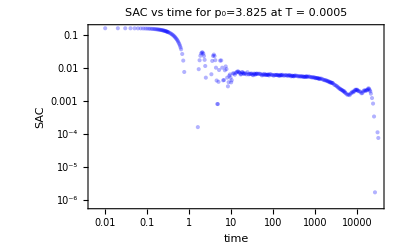

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={4.24*10^(-4),8.13*10^(-4),8.69*10^(-4),1.45*10^(-4),1.33*10^(-4),8.15*10^(-4),8.31*10^(-5),1.58*10^(-3),4.96*10^(-4),1.45*10^(-3)}
```

{0.000424,0.000813,0.000869,0.000145,0.000133,0.000815,0.0000831,0.00158,0.000496,0.00145}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>20&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{73,73,73,73,73,129,73,129,73,129}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{133,127,125,136,132,244,137,259,128,262}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.65,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.00392842,0.00403569,0.00358133,0.00433638,0.00312314,0.00391859,0.00429439,0.00638568,0.00373983,0.00475457}

0.00420.0009

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{1599.59,1283.92,1362.4,1813.42,791.711,1430.55,1316.44,4074.54,1067.51,3793.08}

1.91.110^3

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.843327,0.870713,0.791799,0.896949,0.862342,0.731581,0.814601,0.919154,0.747099,0.657808}

0.810.08

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.00067

```mathematica
curP=2;curT=15;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={1.11*10^(-3),1.2*10^(-3),7.95*10^(-4),2.01*10^(-3),1.02*10^(-3),7.13*10^(-4),1.79*10^(-3),3.74*10^(-4),9.78*10^(-4),1.68*10^(-3)}
```

{0.00111,0.0012,0.000795,0.00201,0.00102,0.000713,0.00179,0.000374,0.000978,0.00168}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>18&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{72,72,72,72,72,72,72,72,72,72}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{135,116,127,117,132,127,119,138,137,120}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.3,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.00802918,0.00552926,0.00624449,0.00627028,0.00651408,0.00566768,0.00645626,0.00816356,0.00726725,0.00650613}

0.00670.0009

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{982.732,507.439,537.925,754.123,534.964,822.316,763.686,1262.8,1447.55,886.615}

850.312.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.610815,0.778067,0.620403,0.735553,0.50607,0.684593,0.729865,0.673702,0.562771,0.847938}

0.670.10

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.001

```mathematica
curP=2;curT=14;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={1.17*10^(-3),1.51*10^(-3),4.65*10^(-4),1.34*10^(-4),8.06*10^(-4),6.14*10^(-4),2.90*10^(-4),7.12*10^(-4),3.78*10^(-4),1.81*10^(-3)}
```

{0.00117,0.00151,0.000465,0.000134,0.000806,0.000614,0.00029,0.000712,0.000378,0.00181}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>10&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{65,65,65,65,65,65,65,65,65,65}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{123,121,132,108,118,117,116,105,121,108}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.6,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.00001,1.0>G>0.00001,0.012>G>0.00001,1.0>G>0.00001,1.0>G>0.00001,1.0>G>0.00001,1.0>G>0.00001,1.0>G>0.00001,1.0>G>0.00001,1.0>G>0.00001};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.00925636,0.00874759,0.0171158,0.00781231,0.0121638,0.0110411,0.00955047,0.00831936,0.0113511,0.0104529}

0.01060.0027

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{493.147,538.098,519.129,130.213,379.931,331.402,308.239,108.967,237.585,172.948}

322.160.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.608109,0.604581,0.601347,0.931359,0.938758,0.906316,0.931884,0.978961,0.87128,0.714088}

0.810.16

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.0015

```mathematica
curP=2;curT=13;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={2.53*10^(-3),1.75*10^(-3),2.02*10^(-3),2.33*10^(-3),2.91*10^(-3),2.96*10^(-3),5.97*10^(-4),3.44*10^(-3),2.44*10^(-3),1.16*10^(-3)}
```

{0.00253,0.00175,0.00202,0.00233,0.00291,0.00296,0.000597,0.00344,0.00244,0.00116}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>10&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{65,65,65,65,65,65,65,65,65,65}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{99,106,107,98,99,102,99,102,104,96}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={0.8>β>0.4,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0165359,0.0130636,0.0154877,0.0171864,0.0152174,0.0123383,0.0118264,0.015362,0.0196659,0.0128537}

0.01500.0025

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{105.071,139.192,144.949,86.8908,76.4007,151.354,71.9472,98.3676,72.4387,65.4459}

101.33.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.784139,0.729039,0.72663,0.79634,0.719289,0.61794,0.785966,0.66332,0.570434,0.792654}

0.720.08

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],ImageSize->400,Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.002

```mathematica
curP=2;curT=12;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={4.16*10^(-3),1.82*10^(-3),1.03*10^(-3),1.38*10^(-3),3.36*10^(-3),8.56*10^(-4),1.73*10^(-3),1.4*10^(-3),2.47*10^(-3),1.97*10^(-3)}
```

{0.00416,0.00182,0.00103,0.00138,0.00336,0.000856,0.00173,0.0014,0.00247,0.00197}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>9&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{64,64,64,64,64,64,64,64,64,64}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{95,93,99,100,95,101,98,105,103,100}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.8,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0215377,0.0193508,0.0188587,0.016972,0.019716,0.0198617,0.0181758,0.0213552,0.0212409,0.0190957}

0.01960.0015

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{76.3848,59.6633,74.3794,88.9737,75.2845,67.9386,81.5646,76.9299,83.7851,83.0521}

77.8.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.862714,0.995563,0.994537,0.954522,0.627492,0.920594,0.984379,0.620321,0.778213,0.815855}

0.860.14

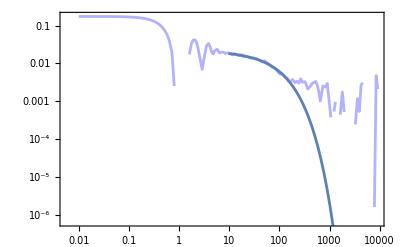
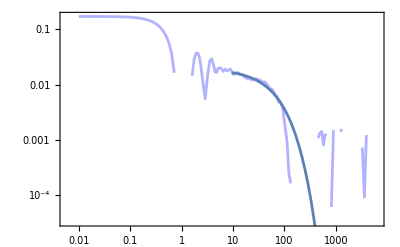
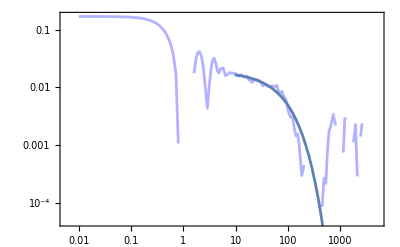
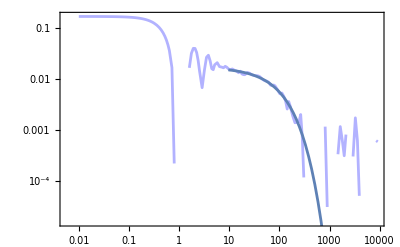
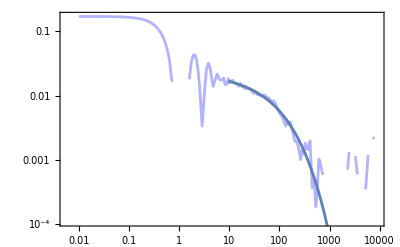
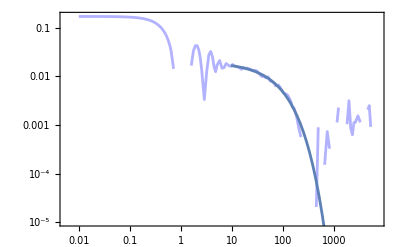
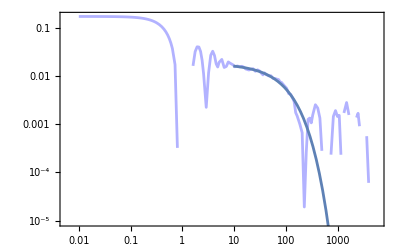
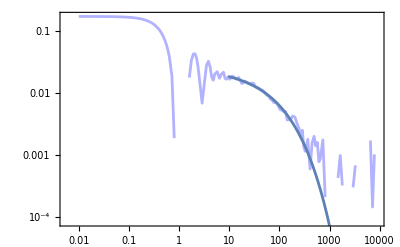

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.0025

```mathematica
curP=2;curT=11;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={3.61*10^(-3),8.52*10^(-4),1.93*10^(-3),4.04*10^(-3),2.14*10^(-3),1.56*10^(-3),2.33*10^(-3),2.97*10^(-3),4.18*10^(-3),2.45*10^(-3)}
```

{0.00361,0.000852,0.00193,0.00404,0.00214,0.00156,0.00233,0.00297,0.00418,0.00245}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>9&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{64,64,64,64,64,64,64,64,64,64}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{99,92,94,95,92,95,96,99,96,97}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.7,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.02,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0301073,0.0259861,0.0236269,0.0242183,0.0239293,0.0243231,0.0271187,0.0209644,0.0233222,0.0241286}

0.02480.0025

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{51.2983,32.2596,34.3132,44.4094,38.7944,27.6609,54.323,65.4904,66.4065,42.0872}

46.13.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.411047,0.989826,0.800029,0.408777,0.738474,0.567637,0.987642,0.497377,0.750576,0.411561}

0.660.23

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.0031

```mathematica
curP=2;curT=10;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={1.16*10^(-3),7.02*10^(-4),2.56*10^(-4),2.67*10^(-3),4.23*10^(-3),3.83*10^(-3),2.49*10^(-3),3.75*10^(-3),2.77*10^(-3),4.75*10^(-3)}
```

{0.00116,0.000702,0.000256,0.00267,0.00423,0.00383,0.00249,0.00375,0.00277,0.00475}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>6&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{59,59,59,59,59,59,59,59,59,59}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{96,102,103,90,91,87,100,88,92,87}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.8,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0314976,0.0297319,0.0329793,0.0294662,0.0280955,0.0302967,0.0323716,0.0286743,0.0321283,0.0273168}

0.03030.0019

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{30.2008,43.115,26.7928,30.4158,50.1226,31.2143,27.6169,39.7748,30.3704,41.0402}

35.8.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.804462,0.804447,0.806062,0.903916,0.944296,0.966399,0.801659,0.973097,0.847485,0.945682}

0.880.07

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.00385

```mathematica
curP=2;curT=9;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={2.04*10^(-3),2.04*10^(-3),3.56*10^(-3),3.31*10^(-3),2.80*10^(-3),2.30*10^(-3),1.84*10^(-3),2.33*10^(-3),2.92*10^(-3),3.89*10^(-3)}
```

{0.00204,0.00204,0.00356,0.00331,0.0028,0.0023,0.00184,0.00233,0.00292,0.00389}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>6&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{59,59,59,59,59,59,59,59,59,59}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{90,88,88,88,87,88,99,84,89,87}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.7,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0354498,0.0314467,0.0344699,0.0408254,0.0357827,0.0351877,0.0436215,0.034816,0.0384098,0.0321889}

0.0360.004

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{27.6769,23.7212,32.2235,28.3528,23.7198,26.6387,30.3981,19.5713,30.0434,32.3079}

27.4.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.987878,0.987612,0.903473,0.977713,0.934302,0.994951,0.701132,0.992091,0.984679,0.980941}

0.940.09

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.005

```mathematica
curP=2;curT=8;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={1.61*10^(-3),1.25*10^(-3),2.59*10^(-3),1.62*10^(-3),3.36*10^(-3),3.43*10^(-3),4.35*10^(-3),7.09*10^(-4),1.31*10^(-3),2.61*10^(-3)}
```

{0.00161,0.00125,0.00259,0.00162,0.00336,0.00343,0.00435,0.000709,0.00131,0.00261}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>6&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{59,59,59,59,59,59,59,59,59,59}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{93,87,89,84,84,90,89,88,85,82}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.7,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.059643,0.0548637,0.0396713,0.0514978,0.04665,0.0394899,0.0578109,0.0420025,0.0341226,0.0382782}

0.0460.009

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{13.588,20.4187,26.8168,15.9383,17.2651,19.3897,11.5641,20.9025,20.2882,18.7408}

18.4.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.719903,0.894576,0.989182,0.946042,0.98295,0.702676,0.701672,0.967517,0.986367,0.991479}

0.890.13

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.0063

```mathematica
curP=2;curT=7;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={1.36*10^(-3),4.49*10^(-3),5.76*10^(-3),3.27*10^(-3),2.73*10^(-3),6.38*10^(-3),4.23*10^(-3),1.95*10^(-3),1.20*10^(-3),2.87*10^(-3)}
```

{0.00136,0.00449,0.00576,0.00327,0.00273,0.00638,0.00423,0.00195,0.0012,0.00287}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>5&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{57,57,57,57,57,57,57,57,57,57}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{87,79,78,84,75,84,83,83,91,79}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.8,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0526086,0.0599328,0.0516236,0.0524798,0.0591219,0.0562339,0.0532522,0.0679706,0.0502625,0.0551933}

0.0560.005

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{10.4608,11.3378,14.9409,8.83357,8.03709,12.9886,10.4934,10.6124,10.3825,13.5259}

11.22.1

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.706939,0.783316,0.973424,0.702072,0.996119,0.701499,0.704107,0.825006,0.702466,0.996001}

0.810.13

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],ImageSize->400,Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.008

```mathematica
curP=2;curT=6;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={2.90*10^(-3),2.29*10^(-3),2.28*10^(-3),3.23*10^(-3),1.86*10^(-3),4.21*10^(-3),1.49*10^(-3),3.76*10^(-3),2.27*10^(-3),2.01*10^(-3)}
```

{0.0029,0.00229,0.00228,0.00323,0.00186,0.00421,0.00149,0.00376,0.00227,0.00201}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>4&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{54,54,54,54,54,54,54,54,54,54}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{77,80,83,80,80,77,80,81,84,79}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.06,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0601467,0.0607595,0.0832486,0.067976,0.061431,0.0685607,0.0710389,0.076532,0.0680496,0.0618043}

0.0680.008

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{10.5305,9.9722,7.0366,9.28612,10.0428,11.7922,9.04279,8.39578,11.1483,9.22306}

9.61.4

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.997398,0.984019,0.667208,0.868397,0.867917,0.997031,0.94291,0.852612,0.844288,0.99354}

0.900.10

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],ImageSize->400,Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.01

```mathematica
curP=2;curT=5;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={2.39*10^(-3),5.90*10^(-3),9.02*10^(-3),3.17*10^(-3),3.75*10^(-3),1.51*10^(-3),3.22*10^(-3),6.27*10^(-3),7.45*10^(-3),1.37*10^(-3)}
```

{0.00239,0.0059,0.00902,0.00317,0.00375,0.00151,0.00322,0.00627,0.00745,0.00137}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>3&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{51,51,51,51,51,51,51,51,51,51}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{79,76,70,73,79,75,75,78,78,77}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.7,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0786588,0.0717054,0.0820067,0.0959531,0.0972096,0.0737329,0.0794704,0.0922656,0.0909059,0.0721754}

0.0830.010

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{8.17162,9.52092,6.29894,4.73409,6.00753,7.31147,7.98753,7.53732,8.00932,8.31898}

7.41.4

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.913744,0.917353,0.958812,0.710617,0.734613,0.994115,0.989155,0.783359,0.701173,0.997687}

0.870.12

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],ImageSize->400,Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.016

```mathematica
curP=2;curT=4;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={4.01*10^(-3),6.19*10^(-4),1.31*10^(-3),2.77*10^(-3),1.74*10^(-3),1.09*10^(-3),1.45*10^(-3),3.59*10^(-3),2.57*10^(-3),2.16*10^(-3)}
```

{0.00401,0.000619,0.00131,0.00277,0.00174,0.00109,0.00145,0.00359,0.00257,0.00216}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>3&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{51,51,51,51,51,51,51,51,51,51}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{69,72,75,75,68,79,71,74,74,69}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.7,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0994701,0.100769,0.0978057,0.129077,0.115379,0.179615,0.099365,0.126004,0.0988605,0.101286}

0.1150.026

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{4.92226,5.07044,5.23683,3.72219,4.49747,2.51206,4.74064,4.07851,5.97835,4.55374}

4.50.9

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.997549,0.998064,0.996965,0.713983,0.998821,0.70111,0.974529,0.71511,0.927059,0.997127}

0.900.13

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],ImageSize->400,Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.03105

```mathematica
curP=2;curT=3;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={7.54*10^(-3),4.94*10^(-3),1.26*10^(-3),1.07*10^(-3),3.18*10^(-3),2.55*10^(-3),3.55*10^(-3),1.37*10^(-3),1.66*10^(-2),1.22*10^(-3)}
```

{0.00754,0.00494,0.00126,0.00107,0.00318,0.00255,0.00355,0.00137,0.0166,0.00122}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>3&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{51,51,51,51,51,51,51,51,51,51}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{59,64,65,67,67,61,64,68,58,65}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.99999,1.0>β>0.8};
plateauConstraints[[curP,curT]]={0.6>G>0.1,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,i]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.194841,0.175521,0.13572,0.167326,0.156958,0.14141,0.132166,0.121241,0.18551,0.158188}

0.1570.024

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{1.89499,2.40369,2.62728,2.43798,2.03609,2.21153,2.43667,2.40791,2.17231,2.46822}

2.310.22

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.981754,0.996548,0.997818,0.998152,0.826511,0.994591,0.991727,0.989345,0.999995,0.991168}

0.980.05

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],ImageSize->400,Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,0.01,100}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.039

```mathematica
curP=2;curT=2;
```

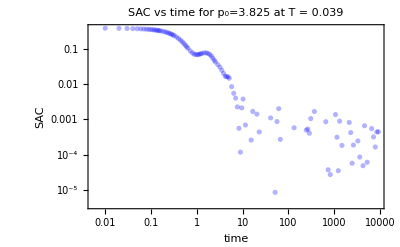
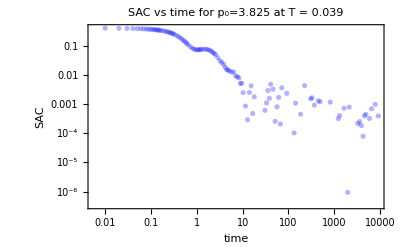
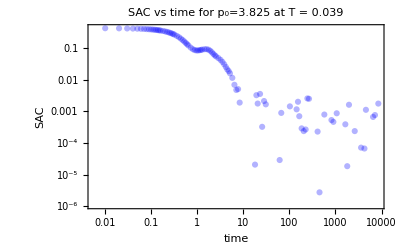
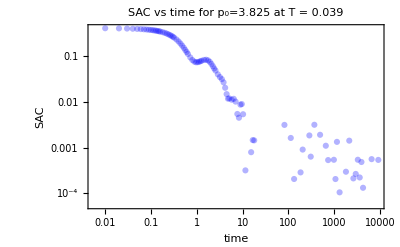
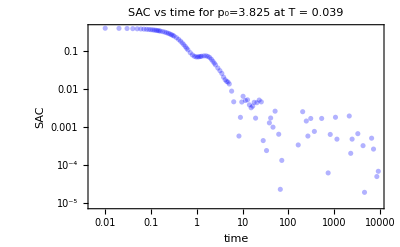
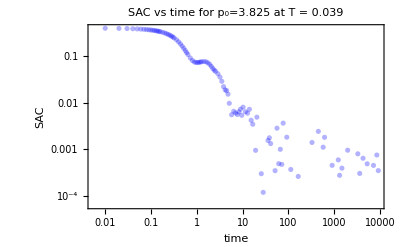
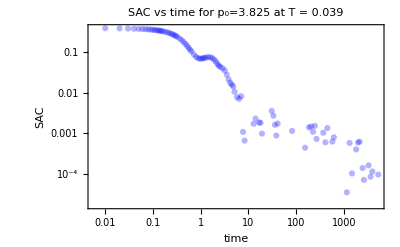
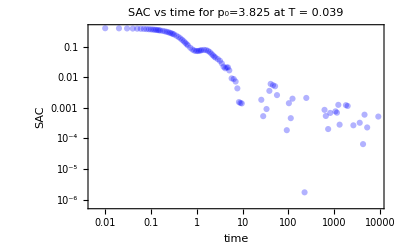

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={1.17*10^(-4),1.55*10^(-2),1.88*10^(-3),1.18*10^(-2),4.66*10^(-3),5.54*10^(-3),6.56*10^(-4),1.41*10^(-3),1.07*10^(-3),1.98*10^(-3)}
```

{0.000117,0.0155,0.00188,0.0118,0.00466,0.00554,0.000656,0.00141,0.00107,0.00198}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>3&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{51,51,51,51,51,51,51,51,51,51}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{64,56,63,57,61,59,63,65,61,66}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=1.;
betaConstraints[[curP,curT]]={1.0>β>0.9999,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.99999,1.0>β>0.8};
plateauConstraints[[curP,curT]]={0.2>G>0.1,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.145037,0.154707,0.199567,0.199184,0.180131,0.199151,0.198335,0.138002,0.199194,0.140817}

0.1750.027

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{2.04645,1.99714,2.01503,1.83626,1.82055,1.80971,1.79479,2.27942,1.71493,2.46127}

1.980.24

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.99995,0.99995,0.999951,0.99995,0.99995,0.999951,0.99995,0.99995,0.999951,0.99995}

0.99995035

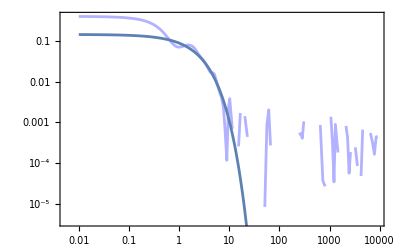
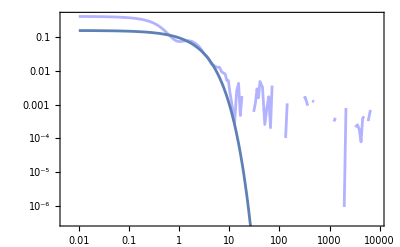
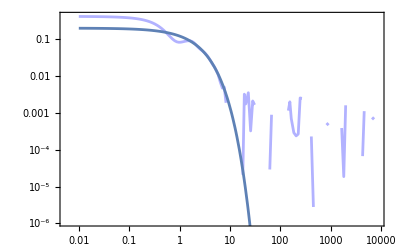
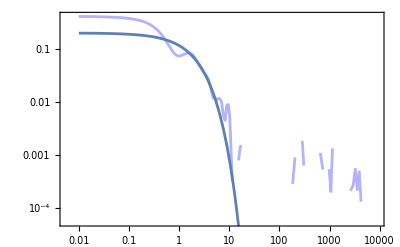
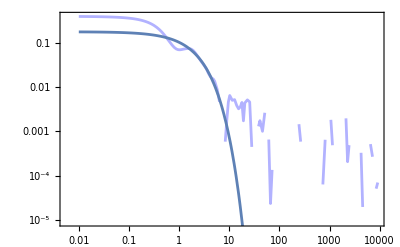
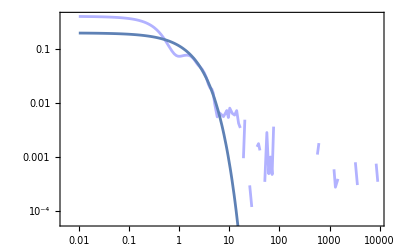
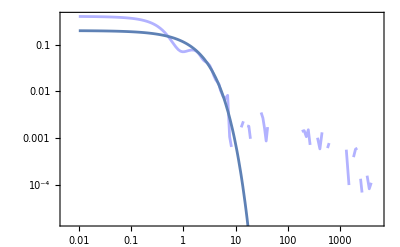
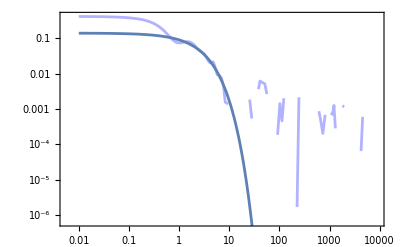
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],ImageSize->400,Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,0.01,100}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.063

```mathematica
curP=2;curT=1;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={4.79*10^(-3),9.06*10^(-3),2.59*10^(-3),3.57*10^(-2),4.71*10^(-3),2.27*10^(-3),6.90*10^(-4),2.58*10^(-3),1.19*10^(-2),3.19*10^(-3)}
```

{0.00479,0.00906,0.00259,0.0357,0.00471,0.00227,0.00069,0.00258,0.0119,0.00319}

```mathematica
fitStartNum={0.0873,0.0855,0.0818,0.0804,0.0806,0.0845,0.0843,0.0855,0.0839,0.0819};
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1]]*4096/temperatures[[curP,curT]]],_?(# <fitStartNum[[i]]&)][[1,1]]+5,{i,Length[SAC[[curP,curT]]]}]
```

{42,41,41,41,41,40,41,40,41,40}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{63,58,55,49,53,56,59,59,53,56}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.9999,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.8,1.0>β>0.99999,1.0>β>0.8};
plateauConstraints[[curP,curT]]={0.6>G>0.13,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.17813,0.17079,0.254331,0.150952,0.183766,0.207372,0.177328,0.190052,0.198781,0.21089}

0.1920.028

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{1.5956,1.95956,1.25027,1.78354,1.50262,3450.27,1.62398,1.60461,1.52423,1.39071}

0.31.110^3

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.99995,0.99995,0.99995,0.999951,0.99995,0.99995,0.99995,0.999951,0.99995,0.999951}

0.99995044

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],ImageSize->400,Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,0.01,100}]],{i,Length[SAC[[curP,curT]]]}]
```

### loose constrains

#### fitting results

```mathematica
Table[Dimensions[fittings[[2,T]]],{T,Length[temperatures[[2]]]}]
```

{{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10}}

```mathematica
fittings[[2]]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
fittings[[2]]={{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}};
```

#### fitting parameters

```mathematica
curP=2;
```

```mathematica
tauAlphaResults[[curP]]
```

{1.570.20,1.980.24,2.310.22,4.50.9,7.41.4,9.51.3,12.42.2,18.4.,27.4.,37.7.,46.13.,77.8.,101.33.,322.160.,850.312.,1.91.110^3}

```mathematica
tauAlphaResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}];
plateauResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}];
betaResults[[curP]]=Join[Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}]];
```

```mathematica
ListLogPlot[Table[{1/temperatures[[curP,T]],tauAlphaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

-Graphics-

```mathematica
ListLogPlot[Table[{temperatures[[curP,T]],tauAlphaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

-Graphics-

```mathematica
ListLogLogPlot[Table[{temperatures[[curP,T]],betaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

-Graphics-

```mathematica
ListLogLogPlot[{Table[{temperatures[[curP,T]],plateauResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Table[{temperatures[[curP,T]],plateauGold[[curP,T,1]]},{T,Length[temperatures[[curP]]]}]},PlotRange->All,Joined->True,PlotLabel->"plateau p0="<>ToString[p0s[[curP]]]]
```

-Graphics-

```mathematica
ListLogLogPlot[Table[{plateauResults[[curP,T,1]]/temperatures[[curP,T]]^1.5,tauAlpha[[curP,T,1]]},{T,Length[temperatures[[curP]]]}],PlotRange->All,Joined->False,PlotLabel->"plateau p0="<>ToString[p0s[[curP]]]]
```

-Graphics-

### mean G(t) and fitting

```mathematica
curT=2;curP=2;
```

```mathematica
redBluePlotConfig[Length[temperatures[[curP]]]/2]
```

{RGBColor[1, 0, 0, 1.],RGBColor[Rational[6, 7], 0, Rational[1, 7], 0.9],RGBColor[Rational[5, 7], 0, Rational[2, 7], 0.8],RGBColor[Rational[4, 7], 0, Rational[3, 7], 0.7],RGBColor[Rational[3, 7], 0, Rational[4, 7], 0.6000000000000001],RGBColor[Rational[2, 7], 0, Rational[5, 7], 0.5],RGBColor[Rational[1, 7], 0, Rational[6, 7], 0.4],RGBColor[0, 0, 1, 0.30000000000000004]}

```mathematica
meanSAC=Table[Table[Mean[Table[SAC[[curP,T,i,1,rec]],{i,10}]],{rec,Min[Table[Length[SAC[[curP,T,i,1]]],{i,10}]]}],{T,Length[temperatures[[curP]]]}];
```

```mathematica
fitStart={42,49,52,57,58,59,60,63,65,65,62,62,62,62,73,73};
fitEnd={58,65,64,73,80,79,87,85,89,94,97,98,101,111,118,127};
betaCons={0.999>β>0.3,0.999>β>0.98,0.999>β>0.3,0.999>β>0.3,0.999>β>0.85,0.999>β>0.3,0.999>β>0.8,0.999>β>0.3,0.85>β>0.3,0.999>β>0.3,0.999>β>0.8,0.85>β>0.3,0.85>β>0.78,0.999>β>0.8,0.999>β>0.8,0.85>β>0.6};
gCons={0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001,0.8>G>0.0001};
```

```mathematica
meanfit=Table[NonlinearModelFit[Table[{SAC[[curP,T,1,2,rec]],meanSAC[[T,rec]]*4096/temperatures[[curP,T]]},{rec,fitStart[[T]],fitEnd[[T]]}],{stretchedExp[t,G,τ,β],{betaCons[[T]],gCons[[T]],τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[curP]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
meanfit={FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]};
```

```mathematica
Table[i,{i,{1,2,3,4,5,7,9}}]
```

{1,2,3,4,5,7,9}

```mathematica
meanSAC[[16]]
```

{1.86812×10^-8,1.8675×10^-8,1.8659×10^-8,1.86333×10^-8,1.85979×10^-8,1.85529×10^-8,1.84981×10^-8,1.84338×10^-8,1.836×10^-8,1.82768×10^-8,1.81841×10^-8,1.80822×10^-8,1.79711×10^-8,1.78509×10^-8,1.77217×10^-8,1.75836×10^-8,1.74353×10^-8,1.71655×10^-8,1.68699×10^-8,1.65495×10^-8,1.62054×10^-8,1.58385×10^-8,1.54501×10^-8,1.50414×10^-8,1.46099×10^-8,1.37716×10^-8,1.28802×10^-8,1.19472×10^-8,1.09845×10^-8,1.00039×10^-8,9.01756×10^-9,8.03718×10^-9,7.08122×10^-9,5.25474×10^-9,3.61663×10^-9,2.22849×10^-9,1.13351×10^-9,3.54732×10^-10,-1.05356×10^-10,-2.63923×10^-10,-1.00932×10^-10,8.72642×10^-10,2.21223×10^-9,3.40939×10^-9,4.07212×10^-9,4.01825×10^-9,3.30062×10^-9,2.16245×10^-9,1.00551×10^-9,-3.95603×10^-10,3.6553×10^-11,1.29209×10^-9,1.7152×10^-9,8.18005×10^-10,-4.45846×10^-10,-9.36616×10^-10,-4.9982×10^-10,-1.30878×10^-10,-1.03553×10^-9,-8.8465×10^-10,-8.93376×10^-10,-1.34312×10^-9,-1.13184×10^-9,-1.10815×10^-9,-1.0512×10^-9,-6.62706×10^-10,-3.0623×10^-10,2.16122×10^-11,3.53194×10^-10,6.66008×10^-10,9.35183×10^-10,1.13661×10^-9,1.27704×10^-9,1.36629×10^-9,1.3515×10^-9,1.27401×10^-9,1.10679×10^-9,9.11064×10^-10,6.94787×10^-10,4.56461×10^-10,2.41981×10^-10,-9.4166×10^-11,-2.4264×10^-10,-1.61206×10^-10,1.07979×10^-10,4.67885×10^-10,8.32838×10^-10,1.08187×10^-9,1.16478×10^-9,1.07811×10^-9,8.66303×10^-10,6.13071×10^-10,3.89166×10^-10,2.61841×10^-10,2.50082×10^-10,3.51986×10^-10,5.20906×10^-10,8.07607×10^-10,8.15561×10^-10,5.75193×10^-10,3.60589×10^-10,3.5522×10^-10,4.92152×10^-10,5.80852×10^-10,5.08036×10^-10,3.53162×10^-10,2.67764×10^-10,2.91827×10^-10,3.66326×10^-10,3.84342×10^-10,3.36115×10^-10,2.8768×10^-10,2.93398×10^-10,3.59186×10^-10,3.4825×10^-10,3.48233×10^-10,3.78609×10^-10,3.6355×10^-10,3.52602×10^-10,3.54893×10^-10,3.37759×10^-10,3.14125×10^-10,2.84011×10^-10,2.72772×10^-10,2.79344×10^-10,2.61991×10^-10,2.56142×10^-10,2.5809×10^-10,2.39873×10^-10,2.41513×10^-10,2.21987×10^-10,2.20122×10^-10,2.14321×10^-10,1.99038×10^-10,1.94497×10^-10,1.88991×10^-10,1.84361×10^-10,1.74921×10^-10,1.72257×10^-10,1.85777×10^-10,1.8666×10^-10,1.77266×10^-10,1.83957×10^-10,1.88431×10^-10,1.95261×10^-10,1.94572×10^-10,1.86407×10^-10,1.761×10^-10,1.66763×10^-10,1.68125×10^-10,1.8866×10^-10,1.82208×10^-10,1.8979×10^-10,1.69642×10^-10,1.66697×10^-10,1.70593×10^-10,1.75784×10^-10,1.73345×10^-10,1.86896×10^-10,1.97171×10^-10,1.87746×10^-10,1.49065×10^-10,1.80261×10^-10,1.63124×10^-10,1.45118×10^-10,1.54788×10^-10,1.74865×10^-10,1.72201×10^-10,1.71158×10^-10}

```mathematica
meanSAC[[16]]=Table[Mean[Table[SAC[[curP,16,i,1,rec]],{i,{1,2,3,4,5,7,9}}]],{rec,Min[Table[Length[SAC[[curP,16,i,1]]],{i,{1,2,3,4,5,7,9}}]]}]
```

{1.8612×10^-8,1.86058×10^-8,1.85898×10^-8,1.85642×10^-8,1.85288×10^-8,1.84838×10^-8,1.84292×10^-8,1.83651×10^-8,1.82914×10^-8,1.82083×10^-8,1.81158×10^-8,1.80141×10^-8,1.79031×10^-8,1.77831×10^-8,1.76542×10^-8,1.75164×10^-8,1.73677×10^-8,1.70492×10^-8,1.66974×10^-8,1.63138×10^-8,1.58998×10^-8,1.54567×10^-8,1.49863×10^-8,1.44902×10^-8,1.39646×10^-8,1.2861×10^-8,1.16847×10^-8,1.04519×10^-8,9.17938×10^-9,7.88424×10^-9,6.5835×10^-9,5.29387×10^-9,4.04219×10^-9,1.66672×10^-9,-4.30951×10^-10,-2.16366×10^-9,-3.4706×10^-9,-4.31973×10^-9,-4.7084×10^-9,-4.66204×10^-9,-4.15297×10^-9,-2.48348×10^-9,-2.89607×10^-10,1.70138×10^-9,2.9286×10^-9,3.13088×10^-9,2.38282×10^-9,1.03104×10^-9,-3.5253×10^-10,-1.82845×10^-9,-7.10056×10^-10,1.55427×10^-9,2.59404×10^-9,1.70789×10^-9,2.54478×10^-10,-1.40914×10^-10,7.40277×10^-10,1.47469×10^-9,3.39317×10^-10,6.61733×10^-10,7.07058×10^-10,7.50363×10^-11,3.42468×10^-10,3.0011×10^-10,2.58592×10^-10,4.89713×10^-10,5.77112×10^-10,5.66619×10^-10,5.46226×10^-10,5.2336×10^-10,4.9726×10^-10,4.6125×10^-10,4.44114×10^-10,4.69562×10^-10,4.6215×10^-10,4.7205×10^-10,4.4403×10^-10,4.42974×10^-10,4.53822×10^-10,4.4637×10^-10,4.4894×10^-10,4.5937×10^-10,4.51969×10^-10,4.45637×10^-10,4.37349×10^-10,4.1866×10^-10,4.25929×10^-10,4.24741×10^-10,4.22897×10^-10,4.18796×10^-10,4.10386×10^-10,4.09495×10^-10,4.03073×10^-10,4.00208×10^-10,3.90147×10^-10,3.87004×10^-10,3.82294×10^-10,3.81134×10^-10,3.7479×10^-10,3.68076×10^-10,3.65889×10^-10,3.59372×10^-10,3.47478×10^-10,3.4572×10^-10,3.39327×10^-10,3.27354×10^-10,3.20634×10^-10,3.05516×10^-10,3.02562×10^-10,2.93691×10^-10,2.85988×10^-10,2.85738×10^-10,2.71783×10^-10,2.59576×10^-10,2.45574×10^-10,2.34623×10^-10,2.24187×10^-10,2.13364×10^-10,1.92623×10^-10,1.86118×10^-10,1.76591×10^-10,1.56005×10^-10,1.3676×10^-10,1.22636×10^-10,1.17679×10^-10,1.05231×10^-10,9.86671×10^-11,9.2347×10^-11,8.62759×10^-11,7.4067×10^-11,5.77013×10^-11,4.31686×10^-11,3.48617×10^-11,2.66148×10^-11,1.64717×10^-11,1.07904×10^-11,5.27457×10^-12,-4.63954×10^-12,3.16022×10^-13,-2.42441×10^-12,-1.32538×10^-13,3.37679×10^-13,1.82262×10^-12,1.25091×10^-11,1.87998×10^-11,2.1109×10^-11,1.39683×10^-11,-1.04297×10^-11,-2.02492×10^-11,-5.30655×10^-12,1.57938×10^-11,1.75393×10^-11,2.75832×10^-11,-1.22193×10^-11,-6.34454×10^-12,-8.30848×10^-12,-6.16853×10^-12,7.7474×10^-12,1.55772×10^-11,3.77293×10^-11,1.4967×10^-11,-4.25855×10^-11,1.36674×10^-11,-8.32614×10^-12,-3.46546×10^-11,-1.83446×10^-11,1.44671×10^-11,1.04327×10^-11,7.89351×10^-12}

```mathematica
fitEndPos[[curP]]
```

{{63,58,55,49,53,56,59,59,53,56},{64,56,63,57,61,59,63,65,61,66},{59,64,65,67,67,61,64,68,58,65},{69,72,75,75,68,79,71,74,74,69},{79,76,70,73,79,75,75,78,78,77},{77,80,83,80,80,77,80,81,84,79},{87,79,78,84,75,84,83,83,91,79},{93,87,89,84,84,90,89,88,85,82},{90,88,88,88,87,88,99,84,89,87},{96,102,103,90,91,87,100,88,92,87},{99,92,94,95,92,95,96,99,96,97},{95,93,99,100,95,101,98,105,103,100},{99,106,107,98,99,102,99,102,104,96},{123,121,132,108,118,117,116,105,121,108},{135,116,127,117,132,127,119,138,137,120},{133,127,125,136,132,244,137,259,128,262}}

```mathematica
fitEndPos[[curP]]={{63,58,55,49,53,56,59,59,53,56},{64,56,63,57,61,59,63,65,61,66},{59,64,65,67,67,61,64,68,58,65},{69,72,75,75,68,79,71,74,74,69},{79,76,70,73,79,75,75,78,78,77},{77,80,83,80,80,77,80,81,84,79},{87,79,78,84,75,84,83,83,91,79},{93,87,89,84,84,90,89,88,85,82},{90,88,88,88,87,88,99,84,89,87},{96,102,103,90,91,87,100,88,92,87},{99,92,94,95,92,95,96,99,96,97},{95,93,99,100,95,101,98,105,103,100},{99,106,107,98,99,102,99,102,104,96},{123,121,132,108,118,117,116,105,121,108},{135,116,127,117,132,127,119,138,137,120},{133,127,125,136,132,244,137,259,128,262}};
```

```mathematica
Table[Length[SAC[[curP,16,i,2]]],{i,10}]
```

{169,169,169,169,169,323,169,323,169,323}

```mathematica
ListLogLogPlot[Table[Table[{SAC[[curP,T,3,2,rec]],meanSAC[[T,rec]]*4096/temperatures[[curP,T]]},{rec,Min[fitEndPos[[curP,T]]]+10}],{T,Length[temperatures[[curP]]]}],PlotRange->{{0.1,3000},{0.0005,0.7}},PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]/2],ImageSize->400,Joined->True]
```

-Graphics-

```mathematica
tshows={1,3,4,7,9,11,13,15,16};
```

```mathematica
Table[{SAC[[curP,11,1,2,rec]],4*meanSAC[[11,rec]]*4096/temperatures[[curP,11]]},{rec,Min[fitEndPos[[curP,11]]]+5}]
```

{{0.,0.704961},{0.01,0.704323},{0.02,0.703303},{0.03,0.701901},{0.04,0.70012},{0.05,0.697962},{0.06,0.69543},{0.07,0.692526},{0.08,0.689253},{0.09,0.685616},{0.1,0.68162},{0.11,0.677268},{0.12,0.672565},{0.13,0.667517},{0.14,0.662128},{0.15,0.656406},{0.16,0.650276},{0.18,0.637226},{0.2,0.622951},{0.22,0.607515},{0.24,0.590984},{0.26,0.573429},{0.28,0.554924},{0.3,0.535546},{0.32,0.5152},{0.36,0.472859},{0.4,0.42836},{0.44,0.3824},{0.48,0.335671},{0.52,0.288856},{0.56,0.242618},{0.6,0.197581},{0.64,0.154902},{0.72,0.0760067},{0.8,0.00970508},{0.88,-0.0416059},{0.96,-0.0766305},{1.04,-0.0951663},{1.12,-0.0980033},{1.2,-0.0868157},{1.28,-0.0618214},{1.44,0.00509436},{1.6,0.0810178},{1.76,0.142817},{1.92,0.175435},{2.08,0.174987},{2.24,0.148061},{2.4,0.107792},{2.56,0.0717431},{2.88,0.0380374},{3.2,0.0668953},{3.52,0.114572},{3.84,0.131005},{4.16,0.109886},{4.48,0.0813944},{4.8,0.0722962},{5.12,0.0837134},{5.76,0.0939623},{6.4,0.0788014},{7.04,0.0784364},{7.68,0.0809903},{8.32,0.075397},{8.96,0.0745353},{9.6,0.0768432},{10.24,0.0735918},{11.52,0.0690711},{12.8,0.0678509},{14.08,0.0636181},{15.36,0.0640855},{16.64,0.0596406},{17.92,0.0602216},{19.2,0.0581968},{20.48,0.0574798},{23.04,0.0524986},{25.6,0.0498325},{28.16,0.0481641},{30.72,0.0460678},{33.28,0.0427734},{35.84,0.0407347},{38.4,0.0396773},{40.96,0.0376404},{46.08,0.0348249},{51.2,0.0308273},{56.32,0.0291785},{61.44,0.0278407},{66.56,0.0240899},{71.68,0.0223092},{76.8,0.0203584},{81.92,0.0185919},{92.16,0.0174336},{102.4,0.0149704},{112.64,0.0148539},{122.88,0.0128053},{133.12,0.0112729},{143.36,0.00959407},{153.6,0.00842319},{163.84,0.00868866}}

```mathematica
imageInch=72.;
```

```mathematica
inset=-Graphics-;
```

```mathematica
paperFigure1a=Show[ListLogLogPlot[Table[Table[{SAC[[curP,tshows[[T]],1,2,rec]],meanSAC[[tshows[[T]],rec]]*4096/temperatures[[curP,tshows[[T]]]]},{rec,Min[fitEndPos[[curP,tshows[[T]]]]]+5}],{T,Length[tshows]}],PlotRange->{{0.1,4000},{0.0003,0.7}},LabelStyle->Directive[FontSize->24,FontName->"Arial"],PlotStyle->redBluePlotConfig[Length[tshows]],ImageSize->8imageInch,Joined->True,FrameLabel->{"t","G(t)"},Epilog->{Inset[inset,{5.2,-2.7},Automatic]},FrameTicks->{{{{0.0002,None,0.015},{0.0003,None,0.015},{0.0004,None,0.015},{0.0005,None,0.015},{0.0006,None,0.015},{0.0007,None,0.015},{0.0008,None,0.015},{0.0009,None,0.015},{0.001,"10^-3",0.03},{0.002,None,0.015},{0.003,None,0.015},{0.004,None,0.015},{0.005,None,0.015},{0.006,None,0.015},{0.007,None,0.015},{0.008,None,0.015},{0.009,None,0.015},{0.01,0.01,0.03},{0.02,None,0.015},{0.03,None,0.015},{0.04,None,0.015},{0.05,None,0.015},{0.06,None,0.015},{0.07,None,0.015},{0.08,None,0.015},{0.09,None,0.015},{0.1,0.1,0.03},{0.2,None,0.015},{0.3,None,0.015},{0.4,None,0.015},{0.5,None,0.015},{0.6,None,0.015},{0.7,None,0.015},{0.8,None,0.015},{0.9,None,0.015},{1,1,0.03}},None},{{{0.1,0.1,0.03},{0.2,None,0.015},{0.3,None,0.015},{0.4,None,0.015},{0.5,None,0.015},{0.6,None,0.015},{0.7,None,0.015},{0.8,None,0.015},{0.9,None,0.015},{1,1,0.03},{2,None,0.015},{3,None,0.015},{4,None,0.015},{5,None,0.015},{6,None,0.015},{7,None,0.015},{8,None,0.015},{9,None,0.015},{10,10,0.03},{20,None,0.015},{30,None,0.015},{40,None,0.015},{50,None,0.015},{60,None,0.015},{70,None,0.015},{80,None,0.015},{90,None,0.015},{100,100,0.03},{200,None,0.015},{300,None,0.015},{400,None,0.015},{500,None,0.015},{600,None,0.015},{700,None,0.015},{800,None,0.015},{900,None,0.015},{1000,1000,0.03},{2000,None,0.015},{3000,None,0.015},{4000,None,0.015},{5000,None,0.015},{6000,None,0.015},{7000,None,0.015},{8000,None,0.015},{9000,None,0.015}},None}}],Table[LogLogPlot[meanfit[[tshows[[T]]]][x],{x,0.1,{100,100,100,100,1000,1000,1000,7000,7000}[[T]]},PlotStyle->{redBluePlotConfig[Length[tshows]][[T]],Dashed},PlotStyle->Dashed],{T,Length[tshows]}]]
```

-Graphics-

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/Gt.jpeg",paperFigure1a,ImageResolution->400]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/Gt.jpeg

```mathematica
meanfit={{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}};
```

## p_0=3.80

### T=0.0022

```mathematica
Length[temperatures[[3]]]
```

14

```mathematica
curP=3;curT=14;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
noiseLevel[[curP,curT]]={4.40*10^(-3),8.24*10^(-3),7.27*10^(-3),2.26*10^(-3),1.45*10^(-2),9.15*10^(-3),6.46*10^(-3),7*10^(-3),1.09*10^(-3),6.29*10^(-3)}
```

{0.0044,0.00824,0.00727,0.00226,0.0145,0.00915,0.00646,7/1000,0.00109,0.00629}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>10&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{113,65,65,65,113,65,113,65,65,65}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{218,122,120,124,219,117,219,123,125,114}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.6,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.021538,0.0250808,0.0244201,0.0207681,0.0295039,0.0221916,0.0226292,0.021357,0.0190241,0.0192736}

0.02260.0031

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{606.95,1151.24,891.335,743.823,1723.19,985.435,836.613,1071.94,737.647,561.695}

931.337.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.834464,0.712698,0.71196,0.87551,0.664684,0.636988,0.939963,0.604357,0.788945,0.810068}

0.760.11

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.0025

```mathematica
curP=3;curT=13;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={2.17*10^(-3),2.66*10^(-3),1.35*10^(-3),3.99*10^(-3),4.21*10^(-4),1.04*10^(-2),6.4*10^(-3),1.17*10^(-3),2.46*10^(-3),6.51*10^(-3)}
```

{0.00217,0.00266,0.00135,0.00399,0.000421,0.0104,0.0064,0.00117,0.00246,0.00651}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>7&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{60,60,60,60,103,103,103,60,60,103}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{127,124,130,126,236,223,213,119,121,209}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.6,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0264096,0.0264337,0.0294638,0.0309413,0.0240285,0.0333566,0.0247965,0.0245275,0.022855,0.0231634}

0.02660.0035

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{377.57,620.838,766.469,617.983,432.204,873.67,428.906,444.327,352.189,435.649}

535.177.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.746153,0.674499,0.683818,0.69921,0.707804,0.602056,0.601407,0.867189,0.616546,0.603235}

0.680.08

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.0028

```mathematica
curP=3;curT=12;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={3.29*10^(-3),5.43*10^(-3),3.22*10^(-3),4.53*10^(-3),7.27*10^(-3),3.87*10^(-3),8.15*10^(-3),6.25*10^(-3),5.09*10^(-3),2.58*10^(-3)}
```

{0.00329,0.00543,0.00322,0.00453,0.00727,0.00387,0.00815,0.00625,0.00509,0.00258}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>6&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{100,100,100,100,100,100,100,100,100,100}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{216,216,200,218,201,222,200,205,196,204}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0283122,0.0313355,0.0260707,0.0335374,0.0303449,0.0360262,0.0318438,0.0302818,0.0255379,0.0268944}

0.03000.0034

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{267.595,271.417,181.211,306.173,283.87,373.914,275.022,244.24,202.434,234.51}

264.54.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.610013,0.504513,0.710976,0.667028,0.688679,0.612495,0.678068,0.543258,0.751514,0.813684}

0.660.09

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.0031

```mathematica
curP=3;curT=11;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>" SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={8.28*10^(-3),3.78*10^(-3),5.61*10^(-3),4.01*10^(-3),5.89*10^(-3),6.18*10^(-3),4.04*10^(-3),3.52*10^(-3),4.44*10^(-3),4.12*10^(-3)}
```

{0.00828,0.00378,0.00561,0.00401,0.00589,0.00618,0.00404,0.00352,0.00444,0.00412}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>7&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{103,103,103,103,103,103,103,103,103,103}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{192,197,194,195,193,192,198,200,195,194}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.4,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0340416,0.0305751,0.0319336,0.0290777,0.033888,0.0319207,0.0300231,0.0330414,0.0302506,0.0293754}

0.03140.0018

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{189.906,160.195,140.209,158.396,169.419,165.459,154.506,180.613,147.392,135.913}

160.17.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.68587,0.744643,0.656622,0.856636,0.761239,0.727715,0.772563,0.803226,0.775303,0.654204}

0.740.06

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.00385

```mathematica
curP=3;curT=10;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>" SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={1.21*10^(-2),1.48*10^(-2),7.30*10^(-3),9.98*10^(-3),7.93*10^(-3),1.77*10^(-3),7.52*10^(-3),9.33*10^(-3),4.81*10^(-3),3.88*10^(-3)}
```

{0.0121,0.0148,0.0073,0.00998,0.00793,0.00177,0.00752,0.00933,0.00481,0.00388}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>6&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{59,59,59,59,59,100,100,59,59,59}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{96,99,101,105,95,201,182,107,101,105}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.55,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0429778,0.0571664,0.0402826,0.0548141,0.0424931,0.0539471,0.0425517,0.0499017,0.0525549,0.0422738}

0.0480.006

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{98.0632,82.7543,66.6327,155.309,51.8307,100.724,97.5631,111.074,105.059,128.49}

100.29.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.867197,0.559356,0.550695,0.723449,0.594638,0.550401,0.90616,0.550726,0.995995,0.902135}

0.720.18

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.005

```mathematica
curP=3;curT=9;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>" SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={5.75*10^(-3),7.56*10^(-3),7.56*10^(-3),3.90*10^(-3),4.88*10^(-3),1.14*10^(-3),9.8*10^(-3),1.74*10^(-2),9.3*10^(-3),3.52*10^(-3)}
```

{0.00575,0.00756,0.00756,0.0039,0.00488,0.00114,0.0098,0.0174,0.0093,0.00352}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>5&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{57,57,57,57,97,97,97,57,57,57}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{91,95,93,96,169,174,155,87,94,92}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.45,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0551195,0.0602162,0.0725872,0.0499545,0.0551351,0.0581062,0.0527388,0.0625474,0.0643205,0.0470102}

0.0580.008

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{48.6485,30.6524,43.5003,29.0311,49.9052,50.625,33.8686,49.8174,29.6127,30.4167}

40.10.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.999019,0.554624,0.746421,0.706626,0.874912,0.994773,0.992871,0.827046,0.551259,0.87668}

0.810.17

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.0063

```mathematica
curP=3;curT=8;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>" SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={8.63*10^(-3),8.03*10^(-3),1.92*10^(-2),5.43*10^(-3),3.90*10^(-3),2.04*10^(-2),4.71*10^(-3),3.85*10^(-3),7.08*10^(-3),4.87*10^(-3)}
```

{0.00863,0.00803,0.0192,0.00543,0.0039,0.0204,0.00471,0.00385,0.00708,0.00487}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>5&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{57,57,57,57,97,97,57,97,57,57}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{86,85,84,91,160,145,88,162,91,87}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.7,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.071481,0.0696162,0.0739007,0.07303,0.0647944,0.0771124,0.0668468,0.0589874,0.0631078,0.069742}

0.0690.005

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{25.3959,22.4914,34.3408,21.6415,19.7865,29.8799,28.3634,34.5563,22.5521,22.0555}

26.5.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.85044,0.844496,0.886011,0.701055,0.701172,0.922991,0.883871,0.996571,0.70107,0.854893}

0.830.10

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.008

```mathematica
curP=3;curT=7;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>" SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={1.14*10^(-2),9.74*10^(-3),5.59*10^(-3),1.48*10^(-2),4.71*10^(-3),7.90*10^(-3),6.22*10^(-3),5.14*10^(-3),7.73*10^(-3),8.26*10^(-3)}
```

{0.0114,0.00974,0.00559,0.0148,0.00471,0.0079,0.00622,0.00514,0.00773,0.00826}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>4&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{54,54,54,54,91,91,91,54,54,54}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{81,87,83,82,152,160,160,85,81,86}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.7,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.0757704,0.0890745,0.0782384,0.102479,0.0776914,0.097093,0.0802867,0.0831699,0.0854816,0.083975}

0.0850.009

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{18.0002,24.5877,16.1868,15.4958,16.3437,22.0897,16.8783,15.703,18.0926,19.793}

18.33.0

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.927426,0.833677,0.954023,0.737099,0.922744,0.700711,0.700234,0.761926,0.998758,0.867898}

0.840.11

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.01

```mathematica
curP=3;curT=6;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>" SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={7.14*10^(-3),8.29*10^(-3),5.70*10^(-3),3.38*10^(-3),5.56*10^(-3),4.35*10^(-3),9.77*10^(-3),6.27*10^(-3),4.48*10^(-3),4.52*10^(-3)}
```

{0.00714,0.00829,0.0057,0.00338,0.00556,0.00435,0.00977,0.00627,0.00448,0.00452}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>4&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{54,54,54,54,54,91,91,91,54,54}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{86,77,79,79,78,140,143,144,83,81}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.8,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.089706,0.106918,0.112154,0.0853315,0.0930665,0.0928861,0.107484,0.103292,0.101286,0.0974896}

0.0990.009

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{15.9306,8.41864,9.8745,10.6702,12.3717,11.9065,11.9528,10.3811,12.7162,11.3122}

11.62.0

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.8005,0.803172,0.850718,0.904104,0.998222,0.99934,0.800988,0.8014,0.920103,0.927825}

0.880.08

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.016

```mathematica
curP=3;curT=5;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>" SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={2.51*10^(-3),1.69*10^(-3),8.10*10^(-3),3.19*10^(-3),1.9*10^(-3),1.53*10^(-3),5.33*10^(-3),3.67*10^(-3),3.99*10^(-3),1.60*10^(-3)}
```

{0.00251,0.00169,0.0081,0.00319,0.0019,0.00153,0.00533,0.00367,0.00399,0.0016}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>4&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{54,54,54,54,91,54,91,91,54,54}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{78,76,76,78,134,76,127,143,74,73}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.8,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.153236,0.117682,0.163971,0.165781,0.124588,0.124907,0.119257,0.14266,0.132636,0.147807}

0.1390.018

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{5.35477,5.91271,1.38777,1.34648,6.38441,7.37566,6.07029,2.13147,6.91668,5.59239}

4.82.3

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.841518,0.985734,0.800757,0.800726,0.898108,0.997923,0.997256,0.800152,0.997457,0.998408}

0.910.09

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.025

```mathematica
curP=3;curT=4;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>" SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={5.49*10^(-3),1.32*10^(-3),4.32*10^(-3),1.21*10^(-2),5.55*10^(-3),3.30*10^(-3),4.95*10^(-3),2.38*10^(-3),6.67*10^(-3),5.34*10^(-3)}
```

{0.00549,0.00132,0.00432,0.0121,0.00555,0.0033,0.00495,0.00238,0.00667,0.00534}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>3&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{51,51,51,51,51,84,84,84,51,51}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{68,66,66,73,69,122,118,126,69,69}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.9,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.174152,0.171395,0.199076,0.133474,0.166925,0.134281,0.126207,0.169626,0.16954,0.195138}

0.1640.025

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{3.51488,3.09989,2.98576,4.58349,3.46533,4.83273,4.58194,3.18081,3.46947,2.8314}

3.70.7

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.998488,0.998905,0.995597,0.900306,0.928027,0.996378,0.998762,0.900866,0.903022,0.92208}

0.950.05

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.03105

```mathematica
curP=3;curT=3;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>" SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={5.34*10^(-3),5.64*10^(-3),3.97*10^(-3),2.49*10^(-3),1.45*10^(-3),1.55*10^(-3),4.77*10^(-3),2.41*10^(-3),1.17*10^(-2),1.43*10^(-3)}
```

{0.00534,0.00564,0.00397,0.00249,0.00145,0.00155,0.00477,0.00241,0.0117,0.00143}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>3&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{51,51,51,51,51,51,84,51,51,51}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{66,66,65,66,73,66,119,67,62,66}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.9,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.138959,0.180822,0.167086,0.163249,0.180708,0.199093,0.168415,0.192954,0.216226,0.193773}

0.1800.022

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{3.35037,2.41695,3.27466,2.97275,2.7527,2.58455,3.09657,2.86302,2.77712,2.74523}

2.880.29

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.996681,0.902505,0.998817,0.998772,0.902264,0.999047,0.90135,0.953231,0.997354,0.99891}

0.960.05

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.039

```mathematica
curP=3;curT=2;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>" SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={8.17*10^(-3),6.49*10^(-3),3.66*10^(-3),4.4*10^(-3),1.12*10^(-3),4.75*10^(-3),1.07*10^(-2),4.83*10^(-3),2.9*10^(-3),1.71*10^(-3)}
```

{0.00817,0.00649,0.00366,0.0044,0.00112,0.00475,0.0107,0.00483,0.0029,0.00171}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>2.5&)][[1,1]],{i,Length[SAC[[curP,curT]]]}]
```

{49,49,49,49,49,81,49,81,49,49}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{62,66,68,65,62,107,60,106,64,65}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.99999,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],3>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.196159,0.148111,0.166692,0.169045,0.306466,0.188586,0.210251,0.194925,0.2111,0.197295}

0.200.04

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{2.34961,2.97655,2.89866,2.55365,1.61477,2.18939,1.94426,2.22592,2.02454,2.14646}

2.30.4

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995}

0.9999949994

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### T=0.063

```mathematica
curP=3;curT=1;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->ToString[i]<>" SAC vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->False],{i,Length[SAC[[curP,curT]]]}]
```

```mathematica
noiseLevel[[curP,curT]]={3.9*10^(-3),1.73*10^(-2),6.84*10^(-3),9.53*10^(-3),7.20*10^(-3),8*10^(-3),1.07*10^(-3),8.48*10^(-3),3.89*10^(-3),5.53*10^(-3)}
```

{0.0039,0.0173,0.00684,0.00953,0.0072,1/125,0.00107,0.00848,0.00389,0.00553}

```mathematica
Normal[SAC[[curP,curT,1,2]]]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.36,0.4,0.44,0.48,0.52,0.56,0.6,0.64,0.72,0.8,0.88,0.96,1.04,1.12,1.2,1.28,1.44,1.6,1.76,1.92,2.08,2.24,2.4,2.56,2.88,3.2,3.52,3.84,4.16,4.48,4.8,5.12,5.76,6.4,7.04,7.68,8.32,8.96,9.6,10.24,11.52,12.8,14.08,15.36,16.64,17.92,19.2,20.48,23.04,25.6,28.16,30.72,33.28,35.84,38.4,40.96,46.08,51.2,56.32,61.44,66.56,71.68,76.8,81.92,92.16,102.4,112.64,122.88,133.12,143.36,153.6,163.84,184.32,204.8,225.28,245.76,266.24,286.72,307.2,327.68,368.64,409.6,450.56,491.52,532.48,573.44,614.4,655.36,737.28,819.2,901.12,983.04,1064.96,1146.88,1228.8,1310.72,1474.56,1638.4,1802.24,1966.08,2129.92,2293.76,2457.6,2621.44,2949.12,3276.8,3604.48,3932.16,4259.84,4587.52,4915.2,5242.88,5898.24,6553.6,7208.96,7864.32,8519.68,9175.04}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,2]]],_?(#>1&)][[1,1]]-5,{i,Length[SAC[[curP,curT]]]}]
```

{33,33,33,33,54,54,33,54,33,33}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[SAC[[curP,curT,i,1,fitStartPos[[curP,curT,i]];;]]*4096/temperatures[[curP,curT]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]+fitStartPos[[curP,curT,i]],{i,Length[SAC[[curP,curT]]]}]
```

{62,53,56,60,90,105,61,92,59,57}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=1.;
betaConstraints[[curP,curT]]={1.0>β>0.99999,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],10>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[SAC[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.188222,0.191735,0.203554,0.190177,0.172468,0.169704,0.197733,0.200127,0.210927,0.202324}

0.1930.013

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{1.76869,1.5819,1.49375,1.6903,1.57947,1.63117,1.65286,1.48907,1.47223,1.60408}

1.600.09

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,curT]]]}]]]
```

{0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995}

0.999995001718

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curP,curT,i,2,rec]],SAC[[curP,curT,i,1,rec]]*4096/temperatures[[curP,curT]]},{rec,Length[SAC[[curP,curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,SAC[[curP,curT,i,2,fitStartPos[[curP,curT,i]]]],10000}]],{i,Length[SAC[[curP,curT]]]}]
```

### loose constrains

#### fitting results

```mathematica
fittings[[3]]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
fittings[[3]]={{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}};
```

#### fitting parameters

```mathematica
curP=3;
```

```mathematica
tauAlphaResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}];
plateauResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}];
betaResults[[curP]]=Join[Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}]];
```

```mathematica
ListLogPlot[Table[{1/temperatures[[curP,T]],tauAlphaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

-Graphics-

```mathematica
ListLogPlot[Table[{temperatures[[curP,T]],tauAlphaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

-Graphics-

```mathematica
ListLogLogPlot[Table[{temperatures[[curP,T]],betaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

-Graphics-

```mathematica
ListLogLogPlot[{Table[{temperatures[[curP,T]],plateauResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Table[{temperatures[[curP,T]],plateauGold[[curP,T,1]]},{T,Length[temperatures[[curP]]]}]},PlotRange->All,Joined->True,PlotLabel->"plateau p0="<>ToString[p0s[[curP]]]]
```

-Graphics-

```mathematica
ListLogLogPlot[{Table[{plateauResults[[curP,T,1]]/temperatures[[curP,T]]^1.2,tauAlpha[[curP,T,1]]},{T,Length[temperatures[[curP]]]}],Table[{plateauResults[[2,T,1]]/temperatures[[2,T]]^1.2,tauAlpha[[2,T,1]]},{T,Length[temperatures[[2]]]}]},PlotRange->All,Joined->True]
```

-Graphics-